# A mathematical model for universal semantics (Text mining in German)

### Weinan E and Yajun Zhou

## Introduction

Accompanying the topic extraction and word translation sections in [1], this Mathematica Notebook file is optimized for v11.0, and it will also run on v10.3 and v10.4. Earlier versions of Mathematica do not contain certain text analysis functionalities required for this program.

Unless explicitly stated otherwise, all the routines (word clustering, word cloud plotting and question answering) below are specifically designed for the current work [1], instead of being imported elsewhere.

[1] W. E and Y. Zhou, “A mathematical model for universal semantics,” 2020, arXiv:1907.12293v6 [cs.CL].

## Preparations

Text corpora mentioned below need to be stored in the following directory (or anywhere else that you redesignate)

```mathematica
SetDirectory["D:\\Documents"]
```

D:\Documents

This Mathematica Notebook file MUST BE executed AFTER all the cells in English.nb are evaluated.

### Pride and Prejudice

The full text for a German translation of Jane Austen’s Pride and Prejudice is commercially available from https://www.amazon.de/Stolz-Vorurteil-Roman-Reclam-Taschenbuch-ebook/dp/B01BHWFUX6/

After manual cleansing, we save the text as Stolz und Vorurteil (2) Grawe.txt,  which begins with

Kapitel 1


Es ist eine allgemein anerkannte Tatsache, dass ein alleinstehender Mann im Besitz eines hübschen Vermögens angeblich nichts dringender braucht als eine Frau.

Zwar sind die Gefühle oder A

and ends with

rcy mochte sie ebenso gern wie Elizabeth, und beide bewahrten ihnen zeit ihres Lebens Dankbarkeit dafür, dass sie Elizabeth mit nach Derbyshire genommen und damit ihre Ehe gestiftet hatten.

The current Mathematica Notebook demonstrates the analysis of Pride and Prejudice. For the analysis of other texts in our current work, one needs to prepare text corpora and modify the codes slightly.

### Jane Eyre

The full text  for a German translation of Charlotte Brontë’s Jane Eyre is commercially available from https://www.amazon.com/gp/product/B009XCD1D4/

After manual cleansing, the text begins with

Erstes Kapitel


Es war ganz unmöglich, an diesem Tage einen Spaziergang zu machen. Am Morgen waren wir allerdings während einer ganzen Stunde in den blätterlosen, jungen Anpflanzungen umhergewandert;

and ends with

at mir die Botschaft geschickt. Täglich verkündet Er mir deutlicher: – ›G ewiß, ich komme bald!‹ und stündlich antworte ich Ihm sehnsuchtsvoller: – ›So komm, Jesus Christus! in Ewigkeit, Amen.‹«

Making sure that all the cells in English.nb have been evaluated, you are ready to execute all the cells in this file.

## German (pre- and post-1996 orthographies)

## German stop words

The following list of stop words is essentially based on

snowball.tartarus.org/algorithms/german/stop.txt

plus some other commonly attested adverbs.

```mathematica
GermanStopWords={"aber","alle","allem","allen","aller","alles","als","also","am","an","ander","andere","anderem","anderen","anderer","anderes","anderm","andern","anders","auch","auf","aus","bei","bin","bis","bist","da","damit","dann","das","dass","daß","dasselbe","dazu","dein","deine","deinem","deinen","deiner","deines","dem","demselben","den","denn","denselben","der","derer","derselbe","derselben","des","desselben","dessen","dich","die","dies","diese","dieselbe","dieselben","diesem","diesen","dieser","dieses","dir","doch","dort","du","durch","ein","eine","einem","einen","einer","eines","einig","einige","einigem","einigen","einiger","einiges","einmal","er","es","etwas","euch","euer","eure","eurem","euren","eurer","eures","für","gegen","gewesen","hab","habe","haben","hast","hat","hatte","hatten","hier","hin","hinter","ich","ihm","ihn","ihnen","ihr","ihre","ihrem","ihren","ihrer","ihres","im","immer","immerhin","in","indem","ins","ist","jede","jedem","jeden","jeder","jedes","jene","jenem","jenen","jener","jenes","jetzt","kann","kein","keine","keinem","keinen","keiner","keines","können","könnte","machen","man","manche","manchem","manchen","mancher","manches","mein","meine","meinem","meinen","meiner","meines","mich","mir","mit","muss","musste","nach","nein","nicht","nichts","nimmer","noch","nun","nur","ob","oder","ohne","schon","sehr","sei","seien","sein","seine","seinem","seinen","seiner","seines","seit","selbst","sich","sie","sind","so","solche","solchem","solchen","solcher","solches","soll","sollte","sondern","sonst","soweit","sowie","sowohl","über","um","und","uns","unse","unsem","unsen","unser","unses","unter","usw","viel","vom","von","vor","während","war","waren","warst","was","weg","weil","weiter","welche","welchem","welchen","welcher","welches","wenn","werde","werden","wie","wieder","will","wir","wird","wirst","wo","wollen","wollte","würde","würden","zu","zum","zur","zwar","zwischen"}∪{"gar","ab","kaum","binnen","warum","mehr","mehrere","mehreres","mehre","mehres","ja","wohl","all","na","je","dafür","davon","dabei","daran","darin","darüber","darauf","obwohl","bevor","ebenso","nie","beim","nie","viel","vieles","viele","vielen","soviel","wieviel"}∪{"darf","darfst","dürfe","dürfen","dürfend","dürfest","dürfet","dürft","durfte","dürfte","durften","dürften","durftest","dürftest","durftet","dürftet","gedurft"}∪{"gekonnt","kann","kannst","könne","können","könnend","könnest","könnet","könnt","konnte","könnte","konnten","könnten","konntest","könntest","konntet","könntet"}∪{"gemocht","mag","magst","mochte","möchte","mochten","möchten","mochtest","möchtest","mochtet","möchtet","möge","mögen","mögend","mögest","möget","mögt"}∪{"gemusst","gemußt","muß","muss","müsse","müssen","müssend","müssest","müsset","musst","müsst","musste","müsste","mussten","müssten","musstest","müsstest","musstet","müsstet","mußt","müßt","mußte","müßte","mußten","müßten","mußtest","müßtest","mußtet","müßtet"}∪{"gesollt","soll","solle","sollen","sollend","sollest","sollet","sollst","sollt","sollte","sollten","solltest","solltet"}∪{"gewollt","will","willst","wolle","wollen","wollend","wollest","wollet","wollt","wollte","wollten","wolltest","wolltet"}∪{"gehabt","hab","habe","haben","habend","habest","habet","habt","hast","hat","hatte","hätte","hatten","hätten","hattest","hättest","hattet","hättet"}∪{"geworden","ward","warden","wardest","wardet","wardst","werd","werde","werden","werdend","werdest","werdet","wird","worden","wurde","würde","wurden","würden","wurdest","würdest","wurdet","würdet","wär","wärst"}∪{"getan","tat","täte","taten","täten","tatest","tätest","tatet","tätet","tu","tue","tuen","tuend","tuest","tuet","tun","ture","tust","tut"}∪{"war","warst","waren","wart","wäre","wärest","wären","wäret","seist","seiet"}∪{"unser","unsere","unserem","unseren","unserer","unseres","unserm","unsern","unsre","unsrem","unsren","unsrer","unsres"}∪{"dem","deme","den","denen","der","deren","derer","dern","dero","des","deß","dessen"}∪{"oft","öfter","öftesten"}∪{"manchmal"}∪{"beide","beidem","beiden","beider","beides"}∪{"wenig","wenige","wenigen","weniger","wenigsten","wenigstens"}∪{"los"}∪{"ziemlich"}∪{"ganz","ganze","ganzem","ganzen","ganzer","ganzes"}∪{"sogar"}∪{"gerade"}∪{"deshalb"}∪{"bisher","bislang"}∪{"her","hinein","hinaus","hinauf","hinüber","herüber","her","herein","herab","heran","heraus","herauf"}∪{"zudem","ausserdem","außerdem"}∪{"irgend","irgendein","irgendeine","irgendeinem","irgendeinen","irgendeiner","irgendeines","iregendetwas","irgendjemand","irgendjemandem","irgendjemanden","irgendjemandes","irgendwann","irgendwas","irgendwer","irgendwie","iregendwo","irgendwelcher","irgendwelche","irgendwelches","irgendwelchem","irgendwelchen"}∪{"ausser","außer"}∪{"hindurch","irgendwohin"}∪{"aufs"}∪{"wer","wessen","wem","wen"}∪{"hingegen","dagegen","gegenüber"}∪{"vielleicht","vielmehr"}∪{"vielleicht","vielmehr","sobald"}∪{"dorthin","dahin","hierhin","wohin","dorther"}∪{"hinten"}∪{"desto","solange","zusammen"}∪{"meins","deins","seins"}∪{"falls","vorbei","sonst","umsonst"}∪{"darum","nachdem"}∪{"indem","seitdem","trotz","trotzdem","vordem"}∪{"jemand","jemandem","jemanden","jemandes","jemands","niemand","niemandem","niemanden","niemandes","niemands"}∪{"genug"}∪{"geradezu","obgleich","obzwar","wenngleich","wiewohl"}∪{"allein","weshalb","weswegen","wieso","pro"}∪{"aneinander","aufeinander","auseinander","beieinander","durcheinander","füreinander","einander","gegeneinander","hintereinander","ineinander","miteinander","nacheinander","nebeneinander","übereinander","untereinander","voneinander","voreinander","zueinander"}∪{"herbei","hervor","hierher","woher"}∪{"vorüber","überdies","hinzu","hinweg","empor","zuvor","jedoch","dennoch","stets","hinunter","hinauf","indes","indessen","nie","niemals","wann","danach"}∪{"solche","solchem","solchen","solcher","solches","solch"};
```

We need to add schon (“already”) to the list of stop words, to avoid conflation with schön (“beautiful”) during approximate clustering (which ignores all umlauts). Although the words schon and schön were indeed etymologically related (reminiscent of the adverbial and adjectival uses of the word pretty in English), their current meanings are well separated.

## German test words

Here are a few German words that inflect (more or less) regularly.

```mathematica
kissGermanNounVerb={"Kuss","Kusse","Kusses","Küsschen","Küsse","Küssen","Kuß","küsse","küssen","küssest","küsst","küsste","küsstest","küsstet","geküsst"};
```

```mathematica
appleGerman={"Apfel","Apfels","Äpfel","Äpfelchen","Äpfeln"};
```

```mathematica
busGerman={"Bus","Busses","Busse","Bussen"};penanceGerman={"Buße","Bußen"};
```

```mathematica
studyGermanVerb={"studieren","studierend","studiert","studiere","studierst","studiert","studiere","studierest","studiere","studieret","studierte","studiertest","studiertest","studierte","studiertet","studierten","studier"};
```

```mathematica
dayGerman={"Tag","Tage","Tagen","Tages","Tags"};
```

```mathematica
workGermanNounVerb={"Arbeit","arbeite","arbeiten","Arbeiten","arbeitest","arbeitet","arbeitete","arbeiteten","gearbeitet"};
```

```mathematica
workerGerman={"Arbeiter","Arbeiters","Arbeitern"};
```

```mathematica
workdayGerman={"Arbeitstag","Arbeitstage","Arbeitstagen","Arbeitstages","Arbeitstags"};
```

```mathematica
workplaceGerman={"Arbeitsplatz","Arbeitsplatzes","Arbeitsplatze","Arbeitsplätze","Arbeitsplätzen"};
```

```mathematica
placeGerman = {"Platz", "Platzes", "Platze", "Plätze", "Plätzen"};
```

```mathematica
bigGerman={"groß","große","großem","großen","großer","größere","größerem","größeren","größerer","größeres","großes","gross","größte","größtem","größten","größter","größtes"};
```

```mathematica
freeGerman={"frei","freier","freie","freies","freien","freiem","freierer","freiere","freieres","freieren","freierem","freisten","freister","freiste","freistes","freisten","freistem"};
```

```mathematica
freedomGerman={"Freiheit","Freiheiten"};
```

```mathematica
houseGermanNounVerb={"Haus","Hauses","Hause","Häuser","Häuschen","hausen","hausend","gehaust","hause","haust","hauste","haustest","hauste","haus","hause"};
```

```mathematica
darkGerman={"dunkel","dunkler","dunkle","dunkles","dunklem","dunklen","dunklerer","dunklere","dunkleres","dunklerem","dunkleren","dunkelster","dunkelste","dunkelstes","dunkelstem","dunkelsten"};
```

```mathematica
oilGerman={"Öl","Öles","Öls","Öle","Ölen"};
```

```mathematica
eggGerman={"Ei","Eie","Eier","Eiern","Eies","Eis"};
```

```mathematica
eggyolkGerman={"Eigelb","Eigelbe","Eigelben","Eigelbs"};
```

```mathematica
yellowGerman={"gelb","gelbe","gelbem","gelben","gelber","gelbere","gelberem","gelberen","gelberer","gelberes","gelbes","gelbste","gelbstem","gelbsten","gelbster","gelbstes"};
```

```mathematica
iceGerman={"Eis","Eise","Eises"};
```

```mathematica
GermanSimpleWords=(kissGermanNounVerb∪appleGerman∪busGerman∪penanceGerman∪studyGermanVerb∪dayGerman∪workGermanNounVerb∪workerGerman∪workdayGerman∪workplaceGerman∪placeGerman∪bigGerman∪freeGerman∪freedomGerman∪houseGermanNounVerb∪darkGerman∪oilGerman∪eggGerman∪eggyolkGerman∪yellowGerman∪iceGerman);
```

Like English, German has hundreds of irregular verbs in daily use. Unlike English, these German verbs may not only have irregular past tense and past participles, but also have irregular present tense conjugations. In the following, we list some typical German irregular verbs with various vowel alternation patterns across different tenses and moods. Our lists below also include some irregular subjunctive forms, which are rarely encountered in modern documents.

```mathematica
commandGerman={"befahl","befähle","befahlen","befählen","befählest","befählet","befahlst","befahlt","befehle","befehlen","befehlend","befehlest","befehlet","befehlt","befiehlst","befiehlt","befohlen"};breakGerman={"brach","bräche","brachen","brächen","brächest","brächet","brachst","bracht","breche","brechen","brechend","brechest","brechet","brecht","brich","brichst","bricht","gebrochen"};feedGerman={"fraß","fräße","fraßen","fräßen","fräßest","fräßet","fraßt","fresse","fressen","fressend","fressest","fresset","fresst","friss","frisst","gefressen"};countGerman={"galt","gälte","galten","gälten","galtest","gältest","galtet","gältet","gegolten","gelte","gelten","geltend","geltest","geltet","gilt","giltst","gölte","gölten","göltest","göltet"};takeGerman={"genommen","nahm","nähme","nahmen","nähmen","nähmest","nähmet","nahmst","nahmt","nehme","nehmen","nehmend","nehmest","nehmet","nehmt","nimm","nimmst","nimmt"};blowGerman={"blas","blase","blasen","blasend","blasest","blaset","blast","bläst","blies","bliese","bliesen","bliesest","blieset","bliest","geblasen"};fryGerman={"brät","brate","braten","bratend","bratest","bratet","brätst","briet","briete","brieten","brietest","brietet","gebraten"};walkGerman={"gelaufen","lauf","laufe","laufen","laufend","laufest","laufet","läufst","lauft","läuft","lief","liefe","liefen","liefest","liefet","liefst","lieft"};drinkGerman={"gesoffen","sauf","saufe","saufen","saufend","saufest","saufet","säufst","sauft","säuft","soff","söffe","soffen","söffen","söffest","söffet","soffst","sofft"};shoveGerman={"gestoßen","stieß","stieße","stießen","stießest","stießet","stießt","stoß","stoße","stoßen","stoßend","stoßest","stoßet","stoßt","stößt"};writeGerman={"schreiben","schreibend","geschrieben","schreibe","schreibst","schreibt","schreibest","schreibet","schrieb","schriebst","schriebt","schrieben","schriebe","schriebest","schriebet"};biteGerman={"beiß","beiße","beißen","beißend","beißest","beißet","beißt","biss","bisse","bissen","bissest","bisset","bisst","gebissen"};grabGerman={"gegriffen","greif","greife","greifen","greifend","greifest","greifet","greifst","greift","griff","griffe","griffen","griffest","griffet","griffst","grifft"};rideGerman={"geritten","reite","reiten","reitend","reitest","reitet","ritt","ritte","ritten","rittest","rittet"};resembleGerman={"geglichen","gleich","gleiche","gleichen","gleichend","gleichest","gleichet","gleichst","gleicht","glich","gliche","glichen","glichest","glichet","glichst","glicht"};flyGerman={"flieg","fliege","fliegen","fliegend","fliegest","flieget","fliegst","fliegt","flog","flöge","flogen","flögen","flögest","flöget","flogst","flogt","geflogen"};pullGerman={"gezogen","zieh","ziehe","ziehen","ziehend","ziehest","ziehet","ziehst","zieht","zog","zöge","zogen","zögen","zögest","zöget","zogst","zogt"};closeGerman={"geschlossen","schließ","schließe","schließen","schließend","schließest","schließet","schließt","schloss","schlösse","schlossen","schlössen","schlossest","schlössest","schlosset","schlösset","schlosst"};creepGerman={"gekrochen","kriech","krieche","kriechen","kriechend","kriechest","kriechet","kriechst","kriecht","kroch","kröche","krochen","kröchen","kröchest","kröchet","krochst","krocht"};findGerman={"fand","fände","fanden","fänden","fandest","fändest","fandet","fändet","finde","finden","findend","findest","findet","gefunden"};beginGerman={"begann","begänne","begannen","begännen","begännest","begännet","begannst","begannt","beginn","beginne","beginnen","beginnend","beginnest","beginnet","beginnst","beginnt","begönne","begonnen","begönnen","begönnest","begönnet"};sleepGerman={"geschlafen","schlaf","schlafe","schlafen","schlafend","schlafest","schlafet","schläfst","schlaft","schläft","schlief","schliefe","schliefen","schliefest","schliefet","schliefst","schlieft"};fallGerman={"fall","falle","fallen","fallend","fallest","fallet","fällst","fallt","fällt","fiel","fiele","fielen","fielest","fielet","fielst","fielt","gefallen"};hangGerman={"gehangen","häng","hänge","hängen","hängend","hängest","hänget","hängst","hängt","hing","hinge","hingen","hingest","hinget","hingst","hingt"};driveGerman={"fahr","fahre","fahren","fahrend","fahrest","fahret","fährst","fahrt","fährt","fuhr","führe","fuhren","führen","führest","führet","fuhrst","fuhrt","gefahren"};readGerman={"gelesen","las","läse","lasen","läsen","läsest","läset","last","lese","lesen","lesend","lesest","leset","lest","lies","liest"};meetGerman={"getroffen","traf","träfe","trafen","träfen","träfest","träfet","trafst","traft","treffe","treffen","treffend","treffest","treffet","trefft","triff","triffst","trifft"};fenceGerman={"fechte","fechten","fechtend","fechtest","fechtet","ficht","fichtst","focht","föchte","fochten","föchten","fochtest","föchtest","fochtet","föchtet","gefochten"};heaveGerman={"gehoben","haben","heb","hebe","heben","hebend","hebest","hebet","hebst","hebt","hob","höbe","hoben","höben","höbest","höbet","hobst","hobt","hübe","hüben","hübest","hübet"};shriekGerman={"gerufen","rief","riefe","riefen","riefest","riefet","riefst","rieft","ruf","rufe","rufen","rufend","rufest","rufet","rufst","ruft"};
```

```mathematica
GermanSampleIrregularVerbs=commandGerman∪breakGerman∪feedGerman∪countGerman∪takeGerman∪blowGerman∪fryGerman∪walkGerman∪drinkGerman∪shoveGerman∪writeGerman∪biteGerman∪grabGerman∪rideGerman∪resembleGerman∪flyGerman∪pullGerman∪closeGerman∪creepGerman∪findGerman∪beginGerman∪sleepGerman∪fallGerman∪hangGerman∪driveGerman∪readGerman∪meetGerman∪fenceGerman∪heaveGerman∪shriekGerman;
```

NOTES:

For clustering German words, it is necessary that we ignore umlauts, so that Apfel (“apple”) is clustered with Äpfel (“apples”) etc. We also need to identify all the occurrences of ß with ss, in order to accommodate to texts written before the German spelling reform in 1996: Kuß (“kiss”, noun, pre-1996), Kuss (“kiss”, noun, post-1996), Küsse (“kisses”, noun, pre- and post-1996). This necessarily carries certain risk, as Buße (“penance”, pre- and post-1996) will be conflated with Busse (“buses”, pre- and post-1996).

All German nouns are capitalized, while adjectives and verbs derived from nouns are not: cf. Deutsch (“German”, noun, “the German language”) and deutsch (“German”, adjective). It is thus advisable to ignore capitalization during clustering (this is contrary to the practice in English, and similar to the case of pre-1948 Danish).

## Approximate clustering of German words

The clustering routine is described below.

### Effective spelling and essential root

```mathematica
GermanEffVowels="a"|"e"|"i"|"o"|"u"|"ê"|"î";
```

```mathematica
GermanEffSpell[w_]:=(prep=StringReplace[StringReplace[StringReplace[ToLowerCase[w],{"porträt":>"poρτρät",WordBoundary~~"gatte"~~""|"n"~~WordBoundary:>"ehemann",WordBoundary~~"gattin"~~""|"nen"~~WordBoundary:>"ehefrau",WordBoundary~~"erinn":>"μνeμnn","hall":>"hσαall","hüll":>"ωρaπ",WordBoundary~~"dent":>"δeνtτ","gef"~~"a"|"ä"~~"hr":>"δaνγρr","irr":>"iιρr","gestalt":>"σηaιπ","hell":>"hχeλl",WordBoundary~~"r"~~"o"|"ö"~~"t":>"roθ","fessel":>"φeσel","fessl":>"φeσl","minut":>"μiνωτ",WordBoundary~~"ach"~~WordBoundary:>"αaχ",WordBoundary~~"gegenwart":>"πρϵsenτ",WordBoundary~~"leah":>"λϵαaη","them":>"θeμ",WordBoundary~~"ri"~~"ss"|"ß":>"ρiφτ","reis":>"ρϵeiσs","recht":>"ρiγχτ",WordBoundary~~"m"~~"u"|"ü"~~"nd":>"μuνδ",WordBoundary~~"blut":>"βλωoδ","leute"~~""|"n"~~WordBoundary:>"mann",WordBoundary~~"schulter":>"schuλδer",WordBoundary~~"roches":>"rρωξϵσ",WordBoundary~~"acht":>"8e","ähn":>"σμähn",WordBoundary~~"bessie":>"βeσθie","welk":>"ωiθρk","dicht":>"θiκt","f"~~"u"|"ü"~~"ss"|"ß":>"φuτσζ","müd":>"μτiρδ",WordBoundary~~"versuch":>"veρσuχ",WordBoundary~~"well":>"oνδαl",WordBoundary~~"gewalt":>"φoρct",WordBoundary~~"helen":>"ϵλeνη","h"~~"a"|"ie"|"ä"~~"lt":>"χoλδ","talent":>"τaλeντ","geheim":>"σeκρeτ",WordBoundary~~"born":>"brunn","feuer":>"φeueρ","weg":>"ωeγ","h"~~"o"|"ö"~~"he":>"hoche",WordBoundary~~"diana":>"διανa",WordBoundary~~"inne":>"ινne",WordBoundary~~"m"~~"ama"|"utti":>"mutter",WordBoundary~~"tot":>"στeρb",WordBoundary~~"tod"~~""|"s"|"es"|"e"|"en"~~WordBoundary:>"στeρb",WordBoundary~~""|"ver"~~"st"~~"a"|"e"|"i"|"o"|"ü"~~"rb":>"στeρb","robert":>"ρoβeρτ","dämmer":>"δaωmeρ","brot":>"βρoτ","meile":>"μϵiλe","quell":>"qveλl",WordBoundary~~"fest":>"φeστ","still":>"σtiλl",WordBoundary~~"gott":>"γoττ",WordBoundary~~"hannah":>"χaννaχ",WordBoundary~~"ree":>"ρϵe","reich":>"ρρeich","plötz":>"σuδδϵν",(c:WordCharacter)~~"sicht":>c<>c<>"siχt",(c0:WordCharacter)~~"kunft":>c0<>ToUpperCase[c0]<>"kunft",(c1:WordCharacter)~~"tr"~~"a"|"ä"~~"cht":>ToUpperCase[c1]<>c1<>"tracht","s"~~"ä"|"a"~~"ss"|"ß":>"sitz",WordBoundary~~"gesessen"~~WordBoundary:>"sitzen",WordBoundary~~"besessen"~~WordBoundary:>"besitzen","relig":>"ρeliγ","b"~~"u"|"ü"~~"ch":>"βuκ","abwesen"~~"h"|"d"~~___:>"αβσenτ","anwesen"~~"h"|"d"~~___:>"πρϵsenτ",WordBoundary~~"mrs"~~WordBoundary:>"zϕρau",WordBoundary~~"benn":>"βenn",WordBoundary~~"de"~~WordBoundary:>"δϵe",WordBoundary~~"jone":>"γιone","ledig":>"σiνγ",WordBoundary~~"gibt"~~WordBoundary:>"geben",WordBoundary~~"gardi":>"γarδi",WordBoundary~~"bald":>"βaλδ","spiel":>"πλal","dame":>"δaμe",WordBoundary~~"lond":>"λonδ","oberst":>"oβerστ",WordBoundary~~"ort":>"ωort",WordBoundary~~"ehe":>"μρe",WordBoundary~~"oa":>"ωa",WordBoundary~~"sommer":>"σoμmer","lied":>"λieδ","pferd":>"χoρσ","wohl":>"whol","liebst":>"lieb"}],{"sitz":>"σitz","setz":>"ζetz",WordBoundary~~"ob":>"ωb","absent":>"αβσenτ","gegess":>"ess","wünsch"~~___:>"wunsç","trän":>"τeαρ","lös":>"λoζ","leist":>"λϵiστ","sonn":>"σoνν",WordBoundary~~"überred":>"πeσβ",WordBoundary~~"brannt":>"brenn",WordBoundary~~"labe"~~WordBoundary:>"λaβ","leb":>"leβ","schock":>"schoκ",WordBoundary~~"ernst":>"erνστ","wasser":>"waσer","verkünd":>"πρoνσ","zoll":>"τoλλ",WordBoundary~~"leib":>"lϵib","fünf":>"5e",WordBoundary~~"vier":>"4e","finger":>"φinγer",WordBoundary~~"gebrochen"~~WordBoundary:>"breçen","schlecht":>"schλecht",WordBoundary~~"miss"~~""|"es"~~WordBoundary:>"μiσ",WordBoundary~~""|"ge"~~"hind":>"χind",(p1:("k"|"sch"|"ss"|"ß"|"ge"))~~"ling":>p1<>"lang","ismus"|("istisch"~~___)~~WordBoundary:>"",(v:"a"|"i")~~"list":>v<>"l","hübe":>"hebe",WordBoundary~~"langsam":>"γλangsam",WordBoundary~~"janu":>"jnu","tz":>"ztz",WordBoundary~~"eb":>"xeb",WordBoundary~~"gesund":>"γesund","wert":>"fwert",WordBoundary~~"bek":>"beκ","vulg":>"xvxulg","wahr":>"vwahr","monat":>"μonat",WordBoundary~~"best"~~(x0:Except["e"]):>"bst"<>x0,"passag":>"paσσag","manier":>"μanier","ruh":>"ρuh",(x:"s"|"a"|"e"|"i"|"o"|"u"|"y"|"k"|"n"|"t"|"p")~~"tisch"~~___:>x<>"ik","welt":>"xwelt","mäd":>"makd",WordBoundary~~""|"ge"~~"gönn":>"goenn","über":>"xüber","bös"|"bosheit"|("boshaft"~~___):>"bboes","'"|"’":>"","ä":>"a","ö":>"o","ü":>"u","ß":>"ss","ei":>"ê","ch":>"ç","bett":>"zbett",WordBoundary~~"last"~~WordBoundary:>"lesen"}],{"beσitz":>"φoρτuν","klag":>"κlag","sçl":>"sçλ","fass":>"φass",WordBoundary~~"lês":>"σoφτ","gew"~~"a"|"i"|"o"~~"nn":>"wiν","wind":>"winδ","hand":>"hanδ","lob":>"λob","lub":>"λub","arb":>"αrb",WordBoundary~~"ort":>"orτ","erb":>"eρβe","grund":>"grunδ",WordBoundary~~"alt":>"aλτ",WordBoundary~~"ohr":>"ohρ",WordBoundary~~"uhr":>"uηρ","tanz":>"taνz","voll":>"ffoll","gast":>"γast","nahr":>"νahr",WordBoundary~~"bus":>"zbus",WordBoundary~~"bes"~~(x:Except["s"|"t"]):>"ges"~~x,"wên":>"xvên",WordBoundary~~"komp":>"comp","tisç":>"τisχ",WordBoundary~~""|"be"~~"str":>"σtr","reçn":>"ρeçn","dien":>"δien","enz"~~""|"en"~~WordBoundary:>"","ement"~~""|"s"~~WordBoundary:>"îren","anz"~~(l:Except["u"]):>"ant"<>l,WordBoundary~~"bat"~~""|"est"|"en"|"et"~~WordBoundary:>"bitten",WordBoundary~~"gebeten"~~WordBoundary:>"bitten",WordBoundary~~"bet":>"ββet",WordBoundary~~"bitter":>"βitter",WordBoundary~~"sass"~~""|"et"|"est"|"t"|"en"~~WordBoundary:>"sitz","satz":>"xσatz","setz":>"zsetz",WordBoundary~~"hu":>"shu","çs"~~(c2:Except["t"]):>"x"<>c2,"çs"~~WordBoundary:>"x",WordBoundary~~"raf":>"ρaf","bild":>"βild","mutter":>"μuther","wort":>"wvort",WordBoundary~~"kam"~~""|"e"|"st"|"en"|"t"|"est"|"et"~~WordBoundary:>"komm","komi":>"κomi",WordBoundary~~"rest":>"ρest","fund"~~(c0:Except["e"]):>"φund"<>c0,WordBoundary~~"tante"~~""|"n"~~WordBoundary:>"τante","dumm":>"δumm","stamm":>"σtamm","stemm":>"σztemm",WordBoundary~~"ahn":>"xzahn","zêt":>"zzêt","siçt":>"σiçt","lêd":>"λêd","platz":>"pplatz",WordBoundary~~"verg":>"verzug","lass"|"liess":>"λass","lock":>"λock","sçon":>"zsçon",WordBoundary~~"gel"~~"a"|"i"|"u"~~"ng":>"geλing",WordBoundary~~"fê":>"fvê","gruss":>"kgruss","winter":>"wvinter","name":>"νame","nummer":>"xnunmmer","froh":>"vroh","w"~~"ê"|"ie"~~"s"~~(c:Except["s"]):>"zxwês"<>c,"w"~~"ê"|"ie"~~"s"~~WordBoundary:>"zxwês","tugend":>"xtugend","saç":>"xsaç","suç":>"zsuç",WordBoundary~~""|"ge"~~"lieb":>"lxieb",WordBoundary~~"oh"~~WordBoundary:>"zxoh","hart":>"xhart","vett":>"vwett","wusst":>"wiss","sieg":>"sxieg","kumm":>"xkumm","kuns":>"gkuns","kund":>"xkund","kind":>"gkind",WordBoundary~~""|"ge"~~"last":>"xlast","list":>"ylist","lust":>"zlust","gut":>"besser","segn":>"szegn",WordBoundary~~"segen"~~""|"s"~~WordBoundary:>"szegn",WordBoundary~~"gehe"|"gehst"|"geht"|"gehen"|"gehest"|"geh"~~WordBoundary:>"ging",WordBoundary~~"mr"~~WordBoundary:>"hherr",WordBoundary~~"herr"~~""|"n"|"en"~~WordBoundary:>"hherr","sohn":>"szohn",WordBoundary~~"abend":>"azbend","folg":>"vfolg","dank":>"thank","ie":>"î","braçte"|"gebraçt":>"bringe","daçt":>"denk","stand":>"steh","in"~~(c:"d"|"g"|"k"):>"în"<>c}];StringReplace[StringReplace[StringTake[prep,UpTo[3]],WordBoundary~~"kam":>"zkam"]<>StringReplace[StringReplace[StringDrop[prep,UpTo[3]],"el":>"l"],{"ln"~~WordBoundary:>"l","haft"|"massig"|"ffoll"|"ist"~~___:>""}],{WordBoundary~~"sçλoζ":>"sçλos",(h:(GermanEffVowels~~___))~~(c:(Except[GermanEffVowels,LetterCharacter]|"e"))~~"st"~~WordBoundary:>h<>c,(c1:Except["a"|"e"|"i"|"o"|"u"|"ê"|"î"|"s"])~~"s"~~WordBoundary:>c1,"h"|"k"~~"êt"~~""|"en"~~WordBoundary:>"","ik"~~""|"en"|("er"~~""|"n"|"s")~~WordBoundary:>"","lên"~~""|"s"~~WordBoundary:>"",(x:Except[GermanEffVowels])~~"çen"|"ling"~~""|"s"|"e"|"en"~~WordBoundary:>x}])
```

```mathematica
GermanProtectedRange[word_]:=Max[Last[Last[Join[{{0,0}},StringPosition[word,WordBoundary~~(""|"a"|"e"|"i"|"u"|"ê"|"be"|"er"|"zer"|"ge"|"mit"|"naç"|"vor"|"zu"|"xüber"~~Except[GermanEffVowels]...~~Except["e",GermanEffVowels])|(Except[GermanEffVowels]..~~"e")~~Except["a"|"e"|"i"|"u"|"ê"|"î"|"r"]...]]]],Last[Last[Join[{{0,0}},StringPosition[word,"a"|"o"|"u"]]]]]
```

```mathematica
GermanEssRootPreBlot[word_]:=(tag=word;hL=GermanProtectedRange[tag];StringReplace[StringReplace[StringReplace[StringTake[tag,hL]<>StringReplace[StringReplace[StringDrop[tag,hL],{"s"~~WordBoundary:>""}],{"e"~~(("d"|"e"|"m"|"n"|"r"|"st"|"t")...)~~WordBoundary:>""}],WordBoundary~~""|"ab"|"an"|"auf"|"aus"|"bê"|"ên"|("h"~~"er"|"in"~~""|"ên"|"ab"|"an"|"aus"|"auf"|"xüber")|"durç"|"mit"|"naç"|"um"|"vor"|"zu"|"zuruck"|"wêter"|"xüber"|"wider"|"wîder"~~""|"zu"|"ge"~~(t:(___~~GermanEffVowels)):>t],x_~~x_~~"t"|WordBoundary:>x],{(c:Except[GermanEffVowels])~~"t"~~WordBoundary:>c,"nd":>"νd"}])
```

```mathematica
BlotFirstVowelGerman[word_]:=(coverage=StringPosition[word,WordBoundary~~""|"a"|"e"|"i"|"o"|"u"|"ê"|"be"~~Except[GermanEffVowels]...~~GermanEffVowels..,Overlaps->False];If[coverage≠{},p=Last[Last[coverage]];StringReplacePart[word,"a",{p,p}],word])
```

### Sorting and clustering

```mathematica
ExtractGermanRootSuffixNW[a_,b_]:=(NW=SequenceAlignment[a,b];NW0=NW;SuffixNW=Last[NW];If[!MatchQ[SuffixNW,_List],SuffixNW={"",""},NW=Drop[NW0,-1]];rootNW=StringJoin[Riffle[Cases[NW0,_String],"#"]];NW=If[prep0=Cases[NW,_List];prep0≠{},First[prep0],{""}];)
```

```mathematica
ExtractGermanRootSuffixSW[a_,b_]:=(SW=SequenceAlignment[a,b,Method->"Local"];SW0=SW;SuffixSW=Last[SW];If[!MatchQ[SuffixSW,_List],SuffixSW={"",""},SW=Drop[SW0,-1]];rootSW=StringJoin[Riffle[Cases[SW0,_String],"#"]];SW=If[prep0=Cases[SW,_List];prep0≠{},First[prep0],{""}];)
```

```mathematica
SimpleHeredityTestGerman[a_,b_]:=StringContainsQ[ToLowerCase[a],GermanEffVowels]&&(aL=StringLength[a];bL=StringLength[b];(a==b)||(b==a<>"t")||(b==a<>"d")||(b==a<>LastLetter[a])||((bL>aL≥bL/2)&&((a==StringTake[b,aL])&&MatchQ[StringTake[b,{aL+1}],"e"|"n"|"s"])))
```

```mathematica
AdmissibleGermanSuffixMismatch[root_,Suffix_,Alternation_]:=And@@{((StringMatchQ[Suffix_⟦1⟧,""|(("d"|"e"|"n"|"t")..)|(LastLetter[root]|"bar"|"er"|"in"|"isç"|"st"|"ig"|"liç"|"ung"|"îr"|"sam"|"tum"~~___)]&&StringMatchQ[Suffix_⟦2⟧,""|(("d"|"e"|"n"|"t")..)|(LastLetter[root]|"bar"|"er"|"in"|"isç"|"st"|"ig"|"liç"|"ung"|"îr"|"sam"|"tum"~~___)]))||(Suffix=={"îh","og"}||Suffix=={"og","îh"}),((Alternation=={""})&&StringContainsQ[ToLowerCase[root],"a"|"e"|"i"|"o"|"u"|"ê"|"î"|"z"])||MatchQ[Alternation,{"ê","î"}|{"ê","i"}|{"î","o"}|{"au","î"}|{"au","o"}|{"o","u"}|{"a","i"}|{"a","î"}|{"a","u"}|{"î","u"}|{"a","o"}|{"i","o"}|{"e","o"}|{"a","e"}|{"e","i"}|{"a","î"}|{"î","i"}|{"e","î"}|{"ah","i"}|{"eh","i"}|{"ah","o"}|{"eh","o"}]||MatchQ[Reverse[Alternation],{"ê","î"}|{"ê","i"}|{"î","o"}|{"au","î"}|{"au","o"}|{"o","u"}|{"a","i"}|{"a","î"}|{"a","u"}|{"î","u"}|{"a","o"}|{"i","o"}|{"e","o"}|{"a","e"}|{"e","i"}|{"a","î"}|{"î","i"}|{"e","î"}|{"ah","i"}|{"eh","i"}|{"ah","o"}|{"eh","o"}]}
```

```mathematica
GermanHeredityTest[a_,b_]:=SimpleHeredityTestGerman[a,b]||(ExtractGermanRootSuffixNW[a,b];((StringLength[rootNW]+Min[StringLength/@NW]+Min[StringLength/@SuffixNW]≥Max[aL,bL]/2)&&(AdmissibleGermanSuffixMismatch[rootNW,SuffixNW,NW])))||(ExtractGermanRootSuffixSW[a,b];((StringLength[rootSW]+Min[StringLength/@SW]+Min[StringLength/@SuffixSW]≥Max[aL,bL]/2)&&(AdmissibleGermanSuffixMismatch[rootSW,SuffixSW,SW])))
```

```mathematica
ApproxClusterGermanFreqList[wfl_]:=(TaggedList=Split[SortBy[{#,prep=GermanEffSpell[#_⟦1⟧],BlotFirstVowelGerman[prep]}&/@wfl,{StringReplace[#_⟦3⟧,"ç":>"ch"],#_⟦2⟧}&],GermanHeredityTest[#1_⟦2⟧,#2_⟦2⟧]&];Transpose[Flatten[#_⟦1⟧&/@#,1]]&/@Split[SortBy[{#_⟦1⟧&/@#,#_⟦1,2⟧,preblot=GermanEssRootPreBlot[#_⟦1,2⟧],BlotFirstVowelGerman[preblot]}&/@TaggedList,{#_⟦4⟧,#_⟦3⟧,#_⟦2⟧}&],(GermanHeredityTest[#1_⟦3⟧,#2_⟦3⟧]||GermanHeredityTest[#1_⟦2⟧,#2_⟦2⟧])&])
```

```mathematica
ApproxClusterGermanFreqList[wfl_]:=(TaggedList=Split[SortBy[{#,prep=GermanEffSpell[#_⟦1⟧],BlotFirstVowelGerman[prep]}&/@wfl,{#_⟦3⟧,#_⟦2⟧}&],GermanHeredityTest[#1_⟦2⟧,#2_⟦2⟧]&];Transpose[Flatten[#_⟦1⟧&/@#,1]]&/@Split[SortBy[{#_⟦1⟧&/@#,#_⟦1,2⟧,preblot=GermanEssRootPreBlot[#_⟦1,2⟧],BlotFirstVowelGerman[preblot]}&/@TaggedList,{#_⟦4⟧,#_⟦3⟧,#_⟦2⟧}&],(GermanHeredityTest[#1_⟦3⟧,#2_⟦3⟧]||GermanHeredityTest[#1_⟦2⟧,#2_⟦2⟧])&])
```

```mathematica
AbsoluteTiming[ClearSystemCache[]; ApproxClusterGermanFreqList[{#,2}&/@GermanSimpleWords]]
```

{0.149217,{{{Ei,Eie,Eier,Eiern,Eies},{2,2,2,2,2}},{{Öl,Öls,Öle,Ölen,Öles},{2,2,2,2,2}},{{Apfel,Äpfel,Äpfelchen,Äpfeln,Apfels},{2,2,2,2,2}},{{Eis,Eise,Eises},{2,2,2}},{{dunkel,dunkle,dunklem,dunklen,dunkler,dunklere,dunklerem,dunkleren,dunklerer,dunkleres,dunkles,dunkelste,dunkelstem,dunkelsten,dunkelster,dunkelstes},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{Eigelb,Eigelbs,Eigelbe,Eigelben},{2,2,2,2}},{{frei,Freiheit,Freiheiten,freie,freiem,freien,freier,freiere,freierem,freieren,freierer,freieres,freies},{2,2,2,2,2,2,2,2,2,2,2,2,2}},{{freiste,freistem,freisten,freister,freistes},{2,2,2,2,2}},{{gelb,gelbe,gelbem,gelben,gelber,gelbere,gelberem,gelberen,gelberer,gelberes,gelbes,gelbste,gelbstem,gelbsten,gelbster,gelbstes},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{groß,gross,große,großem,großen,großer,größere,größerem,größeren,größerer,größeres,großes,größte,größtem,größten,größter,größtes},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{haus,Haus,Häuschen,hause,Hause,hausen,hausend,gehaust,Häuser,Hauses,haust,hauste,haustest},{2,2,2,2,2,2,2,2,2,2,2,2,2}},{{geküsst,küsst,Kuß,Kuss,Küsschen,küsse,Kusse,Küsse,küssest,küssen,Küssen,Kusses,küsste,küsstest,küsstet},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{Platz,Platze,Plätze,Plätzen,Platzes},{2,2,2,2,2}},{{studier,studierst,studiere,studierest,studieren,studierend,studieret,studiert,studierte,studiertest,studierten,studiertet},{2,2,2,2,2,2,2,2,2,2,2,2}},{{Tag,Tags,Tage,Tagen,Tages},{2,2,2,2,2}},{{Bus,Buße,Busse,Bußen,Bussen,Busses},{2,2,2,2,2,2}},{{gearbeitet,Arbeit,arbeite,arbeitest,arbeiten,Arbeiten,Arbeiter,Arbeiters,Arbeitern,arbeitet,arbeitete,arbeiteten},{2,2,2,2,2,2,2,2,2,2,2,2}},{{Arbeitsplatz,Arbeitsplatze,Arbeitsplätze,Arbeitsplätzen,Arbeitsplatzes},{2,2,2,2,2}},{{Arbeitstag,Arbeitstags,Arbeitstage,Arbeitstagen,Arbeitstages},{2,2,2,2,2}}}}

```mathematica
AbsoluteTiming[ClearSystemCache[]; ApproxClusterGermanFreqList[{#,2}&/@GermanSampleIrregularVerbs]]
```

{0.274527,{{{beißt,bisst,beiß,biss,beiße,beißest,bisse,bissest,beißen,bissen,beißend,beißet,bisset,gebissen},{2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{befahl,befahlst,befiehlst,befähle,befählest,befehle,befehlest,befahlen,befählen,befehlen,befohlen,befehlend,befählet,befehlet,befahlt,befehlt,befiehlt},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{begann,begannst,beginn,beginnst,begänne,begännest,beginne,beginnest,begönne,begönnest,begannen,begännen,beginnen,begonnen,begönnen,beginnend,begännet,beginnet,begönnet,begannt,beginnt},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{blas,blies,blase,blasest,bliese,bliesest,blasen,bliesen,blasend,blaset,blieset,blast,bläst,bliest,geblasen},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{brach,brachst,brich,brichst,bräche,brächest,breche,brechest,brachen,brächen,brechen,gebrochen,brechend,brächet,brechet,bracht,bricht},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{brät,brätst,briet,brate,bratest,briete,brietest,braten,brieten,bratend,bratet,brietet,gebraten},{2,2,2,2,2,2,2,2,2,2,2,2,2}},{{brecht},{2}},{{ficht,fichtst,focht,fechte,fechtest,föchte,fochtest,föchtest,fechten,fochten,föchten,fechtend,fechtet,fochtet,föchtet,gefochten},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{fahr,fährst,fuhr,fuhrst,fahre,fahrest,führe,führest,fahren,fuhren,führen,fahrend,fahret,führet,fahrt,fährt,fuhrt},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{fallt,fällt,gefallen,fiel,fielst,fiele,fielest,fielen,fielet,fall,fällst,falle,fallest,fallen,fallend,fallet,fielt},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{fand,fände,fandest,fändest,finde,findest,fanden,fänden,finden,findend,fandet,fändet,findet,gefunden},{2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{flieg,fliegst,flog,flogst,fliege,fliegest,flöge,flögest,fliegen,flogen,flögen,fliegend,flieget,flöget,fliegt,flogt,geflogen},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{fraßt,fresst,frisst,fraß,friss,fräße,fräßest,fresse,fressest,fraßen,fräßen,fressen,fressend,fräßet,fresset,gefressen},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{galt,gilt,giltst,gälte,galtest,gältest,gelte,geltest,gölte,göltest,galten,gälten,gelten,gölten,geltend,galtet,gältet,geltet,göltet,gegolten},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{gleich,gleichst,glich,glichst,gleiche,gleichest,gliche,glichest,gleichen,glichen,gleichend,gleichet,glichet,gleicht,glicht,geglichen},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{greif,greifst,greife,greifest,greifen,greifend,greifet,griff,griffst,griffe,griffest,griffen,griffet,greift,gegriffen,grifft},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{heb,hebst,hob,hobst,hebe,hebest,hübe,hübest,höbe,höbest,haben,heben,hüben,hoben,höben,hebend,hebet,hübet,höbet,hebt,hobt,gehoben},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{gehangen,häng,hängst,hing,hingst,hänge,hängest,hinge,hingest,hängen,hingen,hängend,hänget,hinget,hängt,hingt},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{kriech,kriechst,kroch,krochst,krieche,kriechest,kröche,kröchest,kriechen,krochen,kröchen,kriechend,kriechet,kröchet,kriecht,krocht,gekrochen},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{gelaufen,lauf,läufst,laufe,laufest,laufen,laufend,laufet,lauft,läuft,lief,liefst,liefe,liefest,liefen,liefet,lieft},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{las,lies,läse,läsest,lese,lesest,lasen,läsen,last,lesen,lesend,läset,leset,gelesen,lest,liest},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{nahm,nahmst,nähme,nähmest,nehme,nehmest,nahmen,nähmen,nehmen,nehmend,nähmet,nehmet,nahmt,nehmt,nimm,nimmst,nimmt,genommen},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{rief,riefst,ruf,rufst,riefe,riefest,rufe,rufest,riefen,rufen,rufend,riefet,rufet,rieft,ruft,gerufen},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{reite,reitest,reiten,reitend,reitet,ritt,ritte,rittest,ritten,rittet,geritten},{2,2,2,2,2,2,2,2,2,2,2}},{{sauf,säufst,saufe,saufest,saufen,saufend,saufet,sauft,säuft,soff,soffst,söffe,söffest,soffen,söffen,söffet,gesoffen,sofft},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{schreibst,schrieb,schriebst,schreibe,schreibest,schriebe,schriebest,schreiben,schrieben,schreibend,schreibet,schriebet,schreibt,schriebt,geschrieben},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{geschlafen,schlaf,schläfst,schlief,schliefst,schlafe,schlafest,schliefe,schliefest,schlafen,schliefen,schlafend,schlafet,schliefet,schlaft,schläft,schlieft},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{schließt,schlosst,schließ,schloss,schließe,schließest,schlösse,schlossest,schließen,schlossen,schlössen,schließend,schlössest,schließet,schlosset,schlösset,geschlossen},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{stießt,stoßt,stößt,stieß,stoß,stieße,stießest,stoße,stoßest,stießen,stoßen,stoßend,stießet,stoßet,gestoßen},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{traf,trafst,träfe,träfest,trafen,träfen,träfet,triff,triffst,treffe,treffest,treffen,treffend,treffet,traft,trefft,trifft,getroffen},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{gezogen,zog,zogst,zöge,zögest,zogen,zögen,zöget,zogt,zieh,ziehst,ziehe,ziehest,ziehen,ziehend,ziehet,zieht},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{gefahren},{2}}}}

```mathematica
StringMinus[a_,b_]:=StringDrop[b,StringLength[a]];
```

```mathematica
FindGermanCompounds[KeyRoots_]:=DeleteMissing[If[(StringLength[#_⟦3⟧]≥2)&&StringContainsQ[#_⟦3⟧,GermanEffVowels],t=Flatten[StringCases[KeyRoots,WordBoundary~~#_⟦3⟧|StringReplace[#_⟦3⟧,WordBoundary~~"n"|"e"|"s":>""]|StringReplace[#_⟦3⟧,WordBoundary~~"ge"|"en"|"er"|"es":>""]~~WordBoundary]];If[(Union[t]≠{})&&(Union[t]≠{""}),{#_⟦1⟧,#_⟦2⟧,Union[t]},Missing[]],Missing[]]&/@Flatten[Transpose[{#_⟦2⟧,Table[#_⟦1⟧,Length[#_⟦2⟧]],StringMinus[#_⟦1⟧,#_⟦2⟧]}]&/@DeleteCases[{#,Flatten[StringCases[KeyRoots,WordBoundary~~#~~___]]}&/@KeyRoots,{_,{}}],1]]
```

```mathematica
FindGermanCompounds[{"apfl","apfls","arbêt","arbêtsplatz","arbêtstag","bus","buss","dunkl","ê","êgelb","ês","frê","frêhêt","frêst","gelb","gros","gross","hau","haus","haust","kus","kuss","ol","platz","studîr","studîrt","tag","tags"}]
```

{{arbêtsplatz,arbêt,{platz}},{arbêtstag,arbêt,{tag}},{êgelb,ê,{gelb}}}

```mathematica
ApproxClusterGermanFreqListAssocCompounds[wfl_]:=(TaggedList=Split[SortBy[{#,prep=GermanEffSpell[#_⟦1⟧],BlotFirstVowelGerman[prep]}&/@wfl,{#_⟦3⟧,#_⟦2⟧}&],GermanHeredityTest[#1_⟦2⟧,#2_⟦2⟧]&];CompoundList=Select[{{Union[#_⟦1⟧]_⟦1⟧},#_⟦2⟧}&/@({Union[#_⟦3⟧&/@#],Flatten[#_⟦1⟧&/@#,1]}&/@Split[SortBy[{#_⟦1⟧&/@#,#_⟦1,2⟧,preblot=GermanEssRootPreBlot[#_⟦1,2⟧],BlotFirstVowelGerman[preblot]}&/@TaggedList,{#_⟦4⟧,#_⟦3⟧,#_⟦2⟧}&],(GermanHeredityTest[#1_⟦3⟧,#2_⟦3⟧]||GermanHeredityTest[#1_⟦2⟧,#2_⟦2⟧])&]),((Length[#_⟦1⟧]>0)&&(StringCount[#_⟦1,1⟧,GermanEffVowels]>0))&];KeyRoots=Select[Union[Flatten[#_⟦1⟧&/@CompoundList]],!StringMatchQ[#,"nis"|"u"|"un"|"ung"|"beg"|"beκ"|"bek"|"be"|"ge"|"ên"|"am"|"ab"|"xüber"|"los"|"miss"|"sam"|"bar"|"sçaf"|"sçaft"|"ver"|"vers"|"isç"|"al"|"fal"|"naç"|"mal"|"ar"|"arg"|"gros"|"man"|"tal"]&];CompoundDecomposition=FindGermanCompounds[KeyRoots];DissolvableCompounds={};DissolvedCompounds={};(comp=Cases[CompoundList,{{___,#_⟦1⟧,___},_}]_⟦1⟧;AppendTo[DissolvableCompounds,comp];comphead=Flatten[#_⟦1⟧&/@Cases[CompoundList,{{___,#_⟦2⟧,___},_}]];comptail=Select[Flatten[#_⟦1⟧&/@Cases[CompoundList,{{___,#_⟦3,1⟧,___},_}]],!StringMatchQ[#,"um"|("ung"~~___)|("liç"~~___)|("hêt"~~___)|("kêt"~~___)]&];AppendTo[DissolvedCompounds,{comphead,comp_⟦2⟧}];If[Length[comptail]>0,AppendTo[DissolvedCompounds,{comptail,comp_⟦2⟧}]])&/@CompoundDecomposition;Transpose[Flatten[#_⟦2⟧&/@#,1]]&/@Split[SortBy[Complement[CompoundList∪DissolvedCompounds,DissolvableCompounds],First],#1_⟦1⟧==#2_⟦1⟧&])
```

```mathematica
AbsoluteTiming[ClearSystemCache[]; ApproxClusterGermanFreqListAssocCompounds[{#,2}&/@GermanSimpleWords]]
```

{0.139145,{{{Apfel,Äpfel,Äpfelchen,Äpfeln,Apfels},{2,2,2,2,2}},{{dunkel,dunkle,dunklem,dunklen,dunkler,dunklere,dunklerem,dunkleren,dunklerer,dunkleres,dunkles,dunkelste,dunkelstem,dunkelsten,dunkelster,dunkelstes},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{Eigelb,Eigelbs,Eigelbe,Eigelben,Ei,Eie,Eier,Eiern,Eies},{2,2,2,2,2,2,2,2,2}},{{Eis,Eise,Eises},{2,2,2}},{{frei,Freiheit,Freiheiten,freie,freiem,freien,freier,freiere,freierem,freieren,freierer,freieres,freies},{2,2,2,2,2,2,2,2,2,2,2,2,2}},{{freiste,freistem,freisten,freister,freistes},{2,2,2,2,2}},{{Eigelb,Eigelbs,Eigelbe,Eigelben,gelb,gelbe,gelbem,gelben,gelber,gelbere,gelberem,gelberen,gelberer,gelberes,gelbes,gelbste,gelbstem,gelbsten,gelbster,gelbstes},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{groß,gross,große,großem,großen,großer,größere,größerem,größeren,größerer,größeres,großes,größte,größtem,größten,größter,größtes},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{haus,Haus,Häuschen,hause,Hause,hausen,hausend,gehaust,Häuser,Hauses,haust,hauste,haustest},{2,2,2,2,2,2,2,2,2,2,2,2,2}},{{geküsst,küsst,Kuß,Kuss,Küsschen,küsse,Kusse,Küsse,küssest,küssen,Küssen,Kusses,küsste,küsstest,küsstet},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{Öl,Öls,Öle,Ölen,Öles},{2,2,2,2,2}},{{Arbeitsplatz,Arbeitsplatze,Arbeitsplätze,Arbeitsplätzen,Arbeitsplatzes,Platz,Platze,Plätze,Plätzen,Platzes},{2,2,2,2,2,2,2,2,2,2}},{{studier,studierst,studiere,studierest,studieren,studierend,studieret,studiert,studierte,studiertest,studierten,studiertet},{2,2,2,2,2,2,2,2,2,2,2,2}},{{Arbeitstag,Arbeitstags,Arbeitstage,Arbeitstagen,Arbeitstages,Tag,Tags,Tage,Tagen,Tages},{2,2,2,2,2,2,2,2,2,2}},{{Bus,Buße,Busse,Bußen,Bussen,Busses},{2,2,2,2,2,2}},{{Arbeitsplatz,Arbeitsplatze,Arbeitsplätze,Arbeitsplätzen,Arbeitsplatzes,Arbeitstag,Arbeitstags,Arbeitstage,Arbeitstagen,Arbeitstages,gearbeitet,Arbeit,arbeite,arbeitest,arbeiten,Arbeiten,Arbeiter,Arbeiters,Arbeitern,arbeitet,arbeitete,arbeiteten},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}}}}

## Graphical representation of word clusters

We use the following routines to visualize the word clusters as “bar charts” commonly found in genomic research. Multiple steps are required to convert counts of related words within a cluster into positions and sizes of letter(s) in the bar charts, so as to prepare us for the graphical illustration of the entropy scores received by individual clusters.

We need to leave spaces for various admissible German prefixes.

```mathematica
GermanSort[WordFreqList_]:=Transpose[(assoc=<|#_⟦1⟧->#_⟦2⟧&/@Transpose[WordFreqList]|>;{#,assoc[#]}&/@AlphabeticSort[Keys[assoc],"Swedish"])]
```

```mathematica
RemoveExtraSpace[cl_]:=(sp=Max[0,Min[First[#]_⟦1⟧&/@StringPosition[Transpose[cl]_⟦1⟧,Except[" "],1]-1]];Table[{StringDrop[cl_⟦n,1⟧,sp],cl_⟦n,2⟧},{n,1,Length[cl]}])
```

```mathematica
GermanCompress[w_]:=(Lprot=Max[0,Max[Flatten[StringLength/@StringCases[w," "..]]]];StringTake[#,UpTo[Lprot]]<>StringReplace[StringDrop[#,UpTo[Lprot]],{"ie":>"𝕀","ei":>"𝔼","ss":>"𝕊"}]&/@w)
```

```mathematica
GermanDecompress[w_]:=StringReplace[w,{"𝕀":>"ie","𝔼":>"ei","𝕊":>"ss"}]
```

```mathematica
AdmissibleGermanVerbPrefixes=""|"ab"|"an"|"be"|"auf"|"aus"|"bei"|"ein"|"hin"|"hinein"|"hinaus"|"hinauf"|"hinüber"|"herüber"|"her"|"herein"|"herab"|"heran"|"heraus"|"herauf"|"durch"|"mit"|"nach"|"um"|"vor"|"zu"|"zurück"~~""|"zu"|"ge";
```

```mathematica
PadPrefix0[cl_]:=(HeuristicPrefixL=(Max[#]-1)&/@((Last[#]&/@StringPosition[#,WordBoundary~~AdmissibleGermanVerbPrefixes~~WordCharacter,Overlaps->All])&/@cl_⟦1⟧);MaxPrefixL=Max[HeuristicPrefixL];{Table[{StringDrop[cl_⟦1,n⟧,HeuristicPrefixL_⟦n⟧],StringPadLeft[StringTake[cl_⟦1,n⟧,HeuristicPrefixL_⟦n⟧],MaxPrefixL," "]},{n,1,Length[cl_⟦1⟧]}],cl_⟦2⟧})
```

```mathematica
PadPrefix[cl_]:=GermanSort[RefString=RemoveDiacritics[Last[SortBy[#_⟦1⟧&/@cl_⟦1⟧,StringLength[#]&]],Language->"German"];Transpose[Table[prep=SequenceAlignment[RefString,RemoveDiacritics[cl_⟦1,n,1⟧,Language->"German"]];If[Length[prep_⟦1⟧]>1,Lmax=Max[StringLength/@prep_⟦1⟧];{Table[" ",{m,1,Lmax-StringLength[prep_⟦1,2⟧]}]<>cl_⟦1,n,2⟧<>cl_⟦1,n,1⟧,cl_⟦2,n⟧},{cl_⟦1,n,2⟧<>cl_⟦1,n,1⟧,cl_⟦2,n⟧}],{n,1,Length[cl_⟦1⟧]}]]]
```

```mathematica
ClusterCount={{"ausmachen","machen","ausgemacht","mächtigkeiten"},{10,72,83,100}}
```

{{ausmachen,machen,ausgemacht,mächtigkeiten},{10,72,83,100}}

```mathematica
EvenOut[cl_]:=(prep0=PadPrefix[PadPrefix0[cl]];prep=GermanCompress[prep0_⟦1⟧];L=Max[StringLength[prep]];RemoveExtraSpace[{#_⟦1⟧<>StringJoin[Table[" ",{L-StringLength[#_⟦1⟧]}]],#_⟦2⟧}&/@Transpose[{prep,prep0_⟦2⟧}]])
```

```mathematica
EvenOut[ClusterCount]
```

{{     machen      ,72},{     mächtigk𝔼ten,100},{  ausmachen      ,10},{ausgemacht       ,83}}

```mathematica
SplitEven[ecl_]:=(L=StringLength[ecl_⟦1,1⟧];Table[{m,GermanDecompress[StringTake[#_⟦1⟧,{m}]],#_⟦2⟧}&/@ecl,{m,1,L}]);
```

```mathematica
SplitEven[EvenOut[ClusterCount]]//Transpose//TableForm
```

1
 
72 | 2
 
72 | 3
 
72 | 4
 
72 | 5
 
72 | 6
m
72 | 7
a
72 | 8
c
72 | 9
h
72 | 10
e
72 | 11
n
72 | 12
 
72 | 13
 
72 | 14
 
72 | 15
 
72 | 16
 
72 | 17
 
72
1
 
100 | 2
 
100 | 3
 
100 | 4
 
100 | 5
 
100 | 6
m
100 | 7
ä
100 | 8
c
100 | 9
h
100 | 10
t
100 | 11
i
100 | 12
g
100 | 13
k
100 | 14
ei
100 | 15
t
100 | 16
e
100 | 17
n
100
1
 
10 | 2
 
10 | 3
a
10 | 4
u
10 | 5
s
10 | 6
m
10 | 7
a
10 | 8
c
10 | 9
h
10 | 10
e
10 | 11
n
10 | 12
 
10 | 13
 
10 | 14
 
10 | 15
 
10 | 16
 
10 | 17
 
10
1
a
83 | 2
u
83 | 3
s
83 | 4
g
83 | 5
e
83 | 6
m
83 | 7
a
83 | 8
c
83 | 9
h
83 | 10
t
83 | 11
 
83 | 12
 
83 | 13
 
83 | 14
 
83 | 15
 
83 | 16
 
83 | 17
 
83

```mathematica
Last[SplitEven[EvenOut[ClusterCount]]]
```

{{17, ,72},{17,n,100},{17, ,10},{17, ,83}}

```mathematica
MergeStem[spl_]:=SortBy[(prep=ConnectedComponents[Graph[Join[Table[If[(Length[Union[#_⟦2⟧&/@spl_⟦n⟧]]==1)&&(Length[Union[#_⟦2⟧&/@spl_⟦n+1⟧]]==1),spl_⟦n⟧<->spl_⟦n+1⟧,spl_⟦n⟧<->spl_⟦n⟧],{n,1,Length[spl]-1}],{Last[spl]<->Last[spl]}]]];If[Length[#]>1,{{SortBy[Transpose[#]_⟦1⟧,First]_⟦1,1⟧,StringJoin[#1_⟦2⟧&/@SortBy[Transpose[#]_⟦1⟧,First]],Total[#1_⟦3⟧&/@#_⟦1⟧]}},Flatten[#,1]]&/@prep),First]
```

```mathematica
MergeStem[SplitEven[EvenOut[ClusterCount]]]//TableForm
```

1
 
72 | 1
 
100 | 1
 
10 | 1
a
83
2
 
72 | 2
 
100 | 2
 
10 | 2
u
83
3
 
72 | 3
 
100 | 3
a
10 | 3
s
83
4
 
72 | 4
 
100 | 4
u
10 | 4
g
83
5
 
72 | 5
 
100 | 5
s
10 | 5
e
83
6
m
72 | 6
m
100 | 6
m
10 | 6
m
83
7
a
72 | 7
ä
100 | 7
a
10 | 7
a
83
8
ch
265 |  |  | 
10
e
72 | 10
t
100 | 10
e
10 | 10
t
83
11
n
72 | 11
i
100 | 11
n
10 | 11
 
83
12
 
72 | 12
g
100 | 12
 
10 | 12
 
83
13
 
72 | 13
k
100 | 13
 
10 | 13
 
83
14
 
72 | 14
ei
100 | 14
 
10 | 14
 
83
15
 
72 | 15
t
100 | 15
 
10 | 15
 
83
16
 
72 | 16
e
100 | 16
 
10 | 16
 
83
17
 
72 | 17
n
100 | 17
 
10 | 17
 
83

```mathematica
ColSort[col_]:={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧}&/@Reverse[SortBy[{Flatten[Union[#_⟦1⟧]],Union[#_⟦2⟧]_⟦1⟧,Total[#_⟦3⟧],Min[#_⟦4⟧]}&/@(Transpose[#]&/@(ConnectedComponents[Graph[Join[Table[If[col_⟦k,2⟧==col_⟦k+1,2⟧,{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k+1,1⟧,col_⟦k+1,2⟧,col_⟦k+1,3⟧,k+1},{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}],{k,1,Length[col]-1}],{{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}<->{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}}]]])),Last]]
```

```mathematica
ColSort[#]&/@MergeStem[SplitEven[EvenOut[ClusterCount]]]//TableForm
```

1
a
83 | 1
 
182 |  | 
2
u
83 | 2
 
182 |  | 
3
s
83 | 3
a
10 | 3
 
172 | 
4
g
83 | 4
u
10 | 4
 
172 | 
5
e
83 | 5
s
10 | 5
 
172 | 
6
m
265 |  |  | 
7
a
93 | 7
ä
100 | 7
a
72 | 
8
ch
265 |  |  | 
10
t
83 | 10
e
10 | 10
t
100 | 10
e
72
11
 
83 | 11
n
10 | 11
i
100 | 11
n
72
12
 
93 | 12
g
100 | 12
 
72 | 
13
 
93 | 13
k
100 | 13
 
72 | 
14
 
93 | 14
ei
100 | 14
 
72 | 
15
 
93 | 15
t
100 | 15
 
72 | 
16
 
93 | 16
e
100 | 16
 
72 | 
17
 
93 | 17
n
100 | 17
 
72 |

```mathematica
CumHeight[cl_]:=(ch=0;s={};For[n=1,n<=Length[cl],n++,{s=Join[s,{{cl_⟦n,1⟧,cl_⟦n,2⟧,cl_⟦n,3⟧,ch}}];ch=ch+cl_⟦n,3⟧}];s)
```

```mathematica
CumHeight[(ColSort[#]&/@MergeStem[SplitEven[EvenOut[ClusterCount]]])_⟦6⟧]
```

{{{6},m,265,0}}

```mathematica
Word2BarChart[cl_]:=CumHeight[#]&/@(ColSort[#]&/@MergeStem[SplitEven[EvenOut[cl]]])
```

```mathematica
Word2BarChart[{{"machen","ausmachen","ausgemacht"},{10,72,83}}]//TableForm
```

1
a
83
0 | 1
 
82
83 | 
2
u
83
0 | 2
 
82
83 | 
3
s
83
0 | 3
a
72
83 | 3
 
10
155
4
g
83
0 | 4
u
72
83 | 4
 
10
155
5
e
83
0 | 5
s
72
83 | 5
 
10
155
6
mach
165
0 |  | 
10
t
83
0 | 10
e
82
83 | 
11
 
83
0 | 11
n
82
83 |

## German text mining

### Text normalization

```mathematica
CleanseText[rawtext_]:=StringReplace[StringReplace[rawtext,""|"-"|"—"~~(" "|"\n")...~~"["~~DigitCharacter...~~"]"~~(" "|"\n")...:>""],"u.s.w."|"u. s. w.":>"      "]
```

```mathematica
ExtractGermanTextWords[ExactTitle_]:=(page=StringReplace[ToLowerCase[ToLowerCase[CleanseText[Import[ExactTitle,"HTML"]]]],{{" "..,"\n"..,"--","*","_","–","„","‹","›","(",")","'","’","—","-","«","»","…"}:>" "}];SepWords=ReadList[StringToStream[page],Word,WordSeparators->{" ","\n",",",".",";","?","!",":","\"","(",")","'","’","—","-"}];p=PositionIndex[SepWords];g=StringPosition[AdjustedPage=" "<>StringReplace[page,{{"\n",",",";",":","(",")","'","’","—","-"}:>" ",{".","?","!","\""}:>"  "}]," "..,Overlaps->False];)
```

### Word cluster formation

During cluster formation, we ignore capitalization for approximate clustering of German words.

```mathematica
WordsToClusters[SepWords_]:=(TalLCW=DeleteCases[Tally[ToLowerCase[SepWords]],{Alternatives@@GermanStopWords,_}];m0=TalLCW;ac=ApproxClusterGermanFreqListAssocCompounds[DeleteCases[m0,{"-"|"'",_}]];)
```

The following routine enumerates the nearest pairs of words that start from a member in the upper stream cluster and end in a member in the lower stream cluster.

```mathematica
ShaveSeq[NonVoidSeq_,CutOffLimit_]:=(OutputSeq=NonVoidSeq;While[(OutputSeq≠{})&&(Last[OutputSeq]≥CutOffLimit),OutputSeq=Drop[OutputSeq,-1]];OutputSeq)
```

```mathematica
ShaveSeq[{3851,7265,14307},500]
```

{}

```mathematica
ShaveSeq[{3851,7265,14307},5000]
```

{3851}

```mathematica
ShaveSeq[{3851,7265,14307},8000]
```

{3851,7265}

```mathematica
FindNearestPairs[UpperStream_,LowerStream_]:=(Result={};US=UpperStream;LS=LowerStream;While[(US≠{})&&(LS≠{}),US=ShaveSeq[US,Last[LS]];If[US=={},Break[],Result=Result∪{{Last[US],Last[LS]}};LS=Drop[LS,-1]]];Result)
```

```mathematica
FindNearestPairs[{2416,6666,6814,8220,8349,9031,9464,9848,10019,10629},{3851,7265,14307}]
```

{{2416,3851},{6814,7265},{10629,14307}}

```mathematica
FindNearestPairs[{3851,7265,14307},{2416,6666,6814,8220,8349,9031,9464,9848,10019,10629}]
```

{{3851,6666},{3851,6814},{7265,8220},{7265,8349},{7265,9031},{7265,9464},{7265,9848},{7265,10019},{7265,10629}}

### Word cluster scoring

```mathematica
RecurrenceClusterScore[SepWords_,LowCountCutoff_]:=(pLC=PositionIndex[ToLowerCase[SepWords]];pCluster=<|#->Union[Flatten[pLC/@ToLowerCase[#_⟦1⟧]]]&/@(ac∪({{#_⟦1⟧},{#_⟦2⟧}}&/@Cases[Tally[StringReplace[ToLowerCase[SepWords],WordBoundary~~"i"~~WordBoundary:>"I"]],{Alternatives@@GermanStopWords,_}]))|>;kpCluster=Keys[pCluster];vpCluster=Values[pCluster];WordClusterGap=DeleteMissing[Table[If[Length[vpCluster_⟦i⟧]>LowCountCutoff,{kpCluster_⟦i⟧,Select[Drop[g[[vpCluster_⟦i⟧,2]],1]+1-Drop[g[[vpCluster_⟦i⟧+1,1]],-1]-Max[StringLength/@kpCluster_⟦i,1⟧],#>0&]},Missing[]],{i,1,Length[pCluster]}]];LogLxy=Table[{Transpose[WordClusterGap_⟦i,1⟧],Log[Mean[WordClusterGap_⟦i,2⟧]],Mean[Log[WordClusterGap_⟦i,2⟧]],Length[WordClusterGap_⟦i,2⟧]+1,RefLogMean=Mean[WordClusterGap_⟦i,2⟧Log[WordClusterGap_⟦i,2⟧]]/Mean[WordClusterGap_⟦i,2⟧]-1,Mean[WordClusterGap_⟦i,2⟧Log[WordClusterGap_⟦i,2⟧]^2]/Mean[WordClusterGap_⟦i,2⟧]-2RefLogMean-RefLogMean^2},{i,1,Length[WordClusterGap]}];FragStat=Table[{LogLxy_⟦i,1⟧,Exp[(N[Log[Last[Last[g]]]-LogLxy_⟦i,3⟧,16])-EulerGamma],LogLxy_⟦i,4⟧,If[(LogLxy_⟦i,2⟧-EulerGamma+1/(2(LogLxy_⟦i,4⟧-1))-LogLxy_⟦i,3⟧>(2 √(π^2/6-1-1/(2(LogLxy_⟦i,4⟧-1))))/(√(LogLxy_⟦i,4⟧-1))),"R",If[(LogLxy_⟦i,2⟧-EulerGamma+1/(2(LogLxy_⟦i,4⟧-1))-LogLxy_⟦i,3⟧<-(2 √(π^2/6-1-1/(2(LogLxy_⟦i,4⟧-1))))/(√(LogLxy_⟦i,4⟧-1))),"G","B"]],N[LogLxy_⟦i,5⟧,16],N[LogLxy_⟦i,6⟧,16],N[LogLxy_⟦i,2⟧,16],N[LogLxy_⟦i,3⟧,16]},{i,1,Length[LogLxy]}];)
```

We sort clusters by descending recurrence scores, to prepare for word cloud plots, where the longest word in a cluster occupies an area that is proportional to the recurrence score of the whole cluster.

For the purpose of word cloud plotting, we leave out words with single counts in a document, as well as those words accounting for less than or equal to 5% of the total population within its cluster.

```mathematica
SortWordClusters[ScalingFactor_]:=(AllCluster=Sort[{DeleteCases[DeleteCases[#_⟦1⟧,{_,1}],{_,LessEqualThan[.05#_⟦3⟧]&}],#_⟦2⟧,#_⟦3⟧,#_⟦4⟧,#_⟦5⟧}&/@FragStat,#1[[2]]>#2[[2]]&];SizedWords=Table[Width=Max@StringLength[#_⟦1⟧&/@AllCluster_⟦n,1⟧];ScalingFactor √(AllCluster_⟦n,2⟧/Width)*{Width*0.95,1/0.9},{n,1,Length[AllCluster]}];)
```

We generate TEX codes for the word clouds. (In the TEX preamble, the following line “\newcommand{\BC}[5]{\put(#1,#2){\resizebox{#3\unitlength}{#4\unitlength}{#5}}}” is needed for plotting word barcharts.)

```mathematica
CyrScale=.8;
```

```mathematica
WordClusterCloudPlot:=(FindCenter[SizedWords];MinX=Min[Table[CenterList_⟦n,1⟧-SizedWords_⟦n,1⟧/2,{n,1,Length[SizedWords]}]];MinY=Min[Table[CenterList_⟦n,2⟧-SizedWords_⟦n,2⟧/2,{n,1,Length[SizedWords]}]];MaxX=Max[Table[CenterList_⟦n,1⟧+SizedWords_⟦n,1⟧/2,{n,1,Length[SizedWords]}]];MaxY=Max[Table[CenterList_⟦n,2⟧+SizedWords_⟦n,2⟧/2,{n,1,Length[SizedWords]}]];ArrangedCluster=Table[WCCounts=Transpose[SortBy[AllCluster_⟦n,1⟧,First]];{SizedWords_⟦n⟧,WCCounts_⟦1⟧,WCCounts_⟦2⟧,AllCluster_⟦n,3⟧,AllCluster_⟦n,4⟧,CenterList_⟦n⟧},{n,1,Length[AllCluster]}];Export["PackedWords.txt","\\begin{figure}\\begin{minipage}{\\textwidth}\\fontfamily{pnc}\\selectfont\\begin{spacing}{0}\\begin{picture}("<>ToString[N[Round[MaxX-MinX,10^-3]]]<>","<>ToString[N[Round[MaxY-MinY,10^-3]]]<>")("<>ToString[N[Round[MinX,10^-3]]]<>","<>ToString[N[Round[MinY,10^-3]]]<>"){
"<>StringJoin[Table["\\put("<>ToString[N[Round[ArrangedCluster_⟦k,6,1⟧-ArrangedCluster_⟦k,1,1⟧/2,10^-3]]]<>","<>ToString[N[Round[ArrangedCluster_⟦k,6,2⟧-ArrangedCluster_⟦k,1,2⟧/2,10^-3]]]<>"){\\textcolor"<>If[ArrangedCluster_⟦k,5⟧=="B","[rgb]{0.5,0.5,0.5}{{",If[ArrangedCluster_⟦k,5⟧=="R","{red}{","{green}{"]<>"\\textbf{"]<>"
\\setlength{\\unitlength}{"<>ToString[N[Round[CyrScale*ArrangedCluster_⟦k,1,2⟧,10^-3]]]<>"pt}{
"<>(BCData=Word2BarChart[{ArrangedCluster_⟦k,2⟧,ArrangedCluster_⟦k,3⟧}];H=ArrangedCluster_⟦k,4⟧;StringJoin[Table[Table[If[BCData_⟦m,n,2⟧==" ","","\\BC"<>ToString[BCData_⟦m,n,1⟧-1]<>"{"<>ToString[N[Round[BCData_⟦m,n,4⟧/H,10^-3]]]<>"}{"<>ToString[StringLength[BCData_⟦m,n,2⟧]]<>"}{"<>ToString[N[Round[BCData_⟦m,n,3⟧/H,10^-3]]]<>"}{"<>ToUpperCase[BCData_⟦m,n,2⟧]<>"}\n"],{n,1,Length[BCData_⟦m⟧]}],{m,1,Length[BCData]}]])<>"}}}}
",{k,1,Length[ArrangedCluster]}]]<>"}\\end{picture}\\end{spacing}\\end{minipage}\\end{figure}"];)
```

### Binary transitions

```mathematica
TransitionMeasure[StartWordCluster_,EndWordCluster_,RefBaselineMean_,RefBaselineWidth_]:=(frag=Select[(g[[#_⟦2⟧,2]]+1-g[[#_⟦1⟧+1,1]])&/@FindNearestPairs[pCluster[Transpose[StartWordCluster]],pCluster[Transpose[EndWordCluster]]]-Max[StringLength/@{Transpose[StartWordCluster]_⟦1⟧,Transpose[EndWordCluster]_⟦1⟧}],#>0&];If[Length[frag]>1,WriteRecord={Length[frag],N[Mean[Log[frag]],16]};{WriteRecord_⟦1⟧,WriteRecord_⟦2⟧,(Erf[-(WriteRecord_⟦2⟧-RefBaselineMean)/(√2 √(RefBaselineWidth/WriteRecord_⟦1⟧))]+1)/2},{1,Log[Last[g]_⟦2⟧],0}])
```

```mathematica
TempRGB[t_]:={N[Round[#_⟦1⟧,10^-3]],N[Round[#_⟦2⟧,10^-3]],N[Round[#_⟦3⟧,10^-3]]}&/@(ColorData["TemperatureMap"][t]//InputForm)
```

### Recurrence distribution quartiles

```mathematica
RecurrenceStat[WordCluster_]:=(frag=Select[(g[[#_⟦2⟧,2]]+1-g[[#_⟦1⟧+1,1]])&/@FindNearestPairs[pCluster[Transpose[WordCluster]],pCluster[Transpose[WordCluster]]]-Max[StringLength/@{Transpose[WordCluster]_⟦1⟧}],#>0&];If[Length[frag]>1,Flatten[{Quartiles[frag],{Mean[Exp[Log[N[frag,16]]]],Mean[frag],Max[frag]}}],{0,0,0,0,0,0}])
```

## Pride and Prejudice

### Topic mining by approximate matching of words

We bought the ebooks for German translations of Pride and Prejudice at the Amazon Kindle store.

```mathematica
AbsoluteTiming[ExtractGermanTextWords["Stolz und Vorurteil (2) Grawe.txt"];WordsToClusters[SepWords];RecurrenceClusterScore[SepWords,20];]
```

{34.6195,Null}

```mathematica
CandWordList=Reverse[SortBy[DeleteCases[LogLxy,{{{Alternatives@@GermanStopWords,_}},_,_,_,_,_}],{#_⟦4⟧,#_⟦1,1,1⟧}&]];
```

```mathematica
StemExtract[L_]:=(stem="";list=L;While[(Min[StringLength/@list]>0)&&(Length[Union[StringTake[#,1]&/@list]]==1),{stem=stem<>StringTake[list_⟦1⟧,1],list=StringDrop[#,1]&/@list}];list=#<>If[StringMatchQ[#,stem],"∅",""]&/@L;{stem,StringDrop[#,StringLength[stem]]&/@list})
```

```mathematica
CensorCluster[cl_]:=SortBy[(ordrd=Reverse[SortBy[cl,Last]];TruncPos1=FirstPosition[#==1&/@(#_⟦2⟧&/@ordrd),True];TruncPos=FirstPosition[#<0.05&/@((#_⟦2⟧&/@ordrd)/Accumulate[#_⟦2⟧&/@ordrd]),True];Take[ordrd,Min[DeleteMissing[{TruncPos,TruncPos1}]-1,Length[ordrd]]]),First]
```

```mathematica
ScoredCluster={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧,Total[#_⟦3⟧],#_⟦5⟧}&/@Reverse[SortBy[(prep=Transpose[CensorCluster[#_⟦1⟧]];{#_⟦2⟧,prep_⟦1⟧,prep_⟦2⟧,#_⟦3⟧,#_⟦4⟧})&/@DeleteCases[FragStat,{{{Alternatives@@GermanStopWords,_}},_,_,_,_,_,_,_}],{#_⟦4⟧,#_⟦2⟧}&]];
```

```mathematica
Export["GermanPatterns.txt","\\begin{minipage}{\\textwidth}\n\\noindent\\fontfamily{pnc}\\selectfont\\begin{spacing}{0}
"<>StringJoin[Table["\\textcolor"<>If[ScoredCluster_⟦k,5⟧=="B","[rgb]{0.5,0.5,0.5}{{",If[ScoredCluster_⟦k,5⟧=="R","{red}{","{green}{"]<>"\\textbf{"]<>"\\setlength{\\unitlength}{"<>ToString[N[Round[0.29 √ScoredCluster_⟦k,1⟧,10^-4]]]<>"pt}"<>(BCData=Word2BarChart[{ScoredCluster_⟦k,2⟧,ScoredCluster_⟦k,3⟧}];H=ScoredCluster_⟦k,4⟧;"\\begin{picture}("<>ToString[Total[Max/@StringLength/@(Transpose[#]_⟦2⟧&/@BCData)]]<>","<>ToString[1]<>")\n"<>StringJoin[hpos=0;Table[hinc=Max[StringLength/@Transpose[BCData_⟦m⟧]_⟦2⟧];hpos=hpos+hinc;Table[If[(BCData_⟦m,n,2⟧==" ")||(BCData_⟦m,n,3⟧/H*0.29 √ScoredCluster_⟦k,1⟧<0.15),"","\\BC{"<>ToString[hpos-hinc]<>"}{"<>ToString[N[Round[BCData_⟦m,n,4⟧/H,10^-3]]]<>"}{"<>(ToString[hinc])<>"}{"<>(temp=StringReplace[ToUpperCase[StringReplace[BCData_⟦m,n,2⟧,"ß":>"𝕊"]],"𝕊":>"ß"];ToString[N[Round[BCData_⟦m,n,3⟧/H*If[temp1=StringReplace[temp,{"Œ":>"OE","Æ":>"AE","ß":>"S"}];RemoveDiacritics[temp1,Language->"German"]==temp1,1,1.3],10^-3]]])<>"}{"<>(If[StringDelete[temp,CharacterRange["A","Z"]]=="",temp,StringReplace[StringReplace[StringReplace[ExportString[temp,"TeX"],"\\ss":>"{\\ss}"],___~~"\\[\\text{":>""],"}\\]"~~___:>""]])<>"}\n"],{n,1,Length[BCData_⟦m⟧]}],{m,1,Length[BCData]}]])<>"\\end{picture}}}\n",{k,1,Length[ScoredCluster]}]]<>"\\end{spacing}\\end{minipage}"]
```

GermanPatterns.txt

### Spectral analysis of the transition matrix (non-stop patterns)

```mathematica
NonStopClusters=DeleteCases[Reverse[SortBy[FragStat,#1_⟦3⟧&]],{{___,{Alternatives@@GermanStopWords,_},___},_,_,_,_,_,_,_}];
```

```mathematica
Length[%]
```

520

```mathematica
N0=100;
```

```mathematica
SelectedClusters=Take[NonStopClusters,N0];
```

```mathematica
NonStopClustersGerman=NonStopClusters;
```

```mathematica
Timing[PdeNonStop=Table[Table[prepP=TransitionMeasure[SelectedClusters_⟦m,1⟧,SelectedClusters_⟦n,1⟧,SelectedClusters_⟦m,5⟧,SelectedClusters_⟦m,6⟧],{n,1,Length[SelectedClusters]}],{m,1,Length[SelectedClusters]}];]
```

{70.9688,Null}

```mathematica
Timing[Pde=Table[v=Table[prepP=PdeNonStop_⟦m,n⟧;prepP_⟦1⟧*Exp[-prepP_⟦2⟧],{n,1,Length[SelectedClusters]}];v/Total[v],{m,1,Length[SelectedClusters]}];]
```

{0.046875,Null}

```mathematica
Timing[spec=Eigenvalues[Pde];]
```

{1.29688,Null}

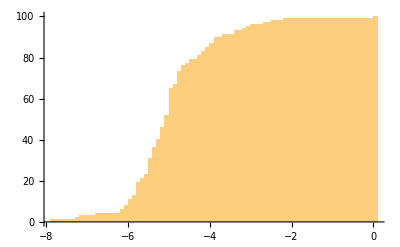

```mathematica
Histogram[Log[Abs[#]]&/@spec,{.1},"CumulativeCount"]
```

```mathematica
hlist=(specAbs=Sort[Log[Abs[#]]&/@spec];Join[{{specAbs_⟦1⟧-1,0}},Transpose[{specAbs,Table[n,{n,1,Length[specAbs]}]}],{{0.5,Length[specAbs]}}]);
```

```mathematica
StringJoin[Table["("<>ToString[N[hlist_⟦n,1⟧]]<>","<>ToString[hlist_⟦n,2⟧]<>")",{n,1,Length[hlist]}]]
```

(-8.85162,0)(-7.85162,1)(-7.22881,2)(-7.18964,3)(-6.72066,4)(-6.19563,5)(-6.19563,6)(-6.09882,7)(-6.09882,8)(-5.98774,9)(-5.93209,10)(-5.93209,11)(-5.87462,12)(-5.87462,13)(-5.72889,14)(-5.72889,15)(-5.72476,16)(-5.72476,17)(-5.71761,18)(-5.71761,19)(-5.67774,20)(-5.67774,21)(-5.55055,22)(-5.55055,23)(-5.47872,24)(-5.47872,25)(-5.47603,26)(-5.47603,27)(-5.41939,28)(-5.41939,29)(-5.41127,30)(-5.41127,31)(-5.33994,32)(-5.33994,33)(-5.31564,34)(-5.3146,35)(-5.3146,36)(-5.24814,37)(-5.24814,38)(-5.23453,39)(-5.23453,40)(-5.19543,41)(-5.19543,42)(-5.1838,43)(-5.1838,44)(-5.13421,45)(-5.13421,46)(-5.07782,47)(-5.07782,48)(-5.01829,49)(-5.01716,50)(-5.01554,51)(-5.01554,52)(-4.96686,53)(-4.96686,54)(-4.96432,55)(-4.95562,56)(-4.95562,57)(-4.92998,58)(-4.92998,59)(-4.9292,60)(-4.9292,61)(-4.92484,62)(-4.92484,63)(-4.91965,64)(-4.91965,65)(-4.80884,66)(-4.80884,67)(-4.76648,68)(-4.76648,69)(-4.76054,70)(-4.76054,71)(-4.75439,72)(-4.75439,73)(-4.67264,74)(-4.67264,75)(-4.67069,76)(-4.52334,77)(-4.41016,78)(-4.41016,79)(-4.27169,80)(-4.27169,81)(-4.14155,82)(-4.14155,83)(-4.07578,84)(-4.07578,85)(-3.92078,86)(-3.92078,87)(-3.83102,88)(-3.82976,89)(-3.82976,90)(-3.65389,91)(-3.3634,92)(-3.3634,93)(-3.13446,94)(-3.04725,95)(-2.9458,96)(-2.63491,97)(-2.40051,98)(-2.14368,99)(0.,100)(0.5,100)

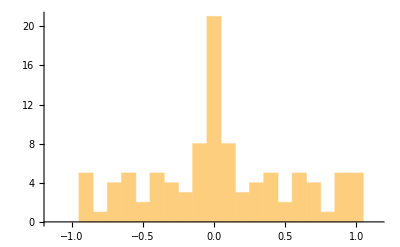

```mathematica
Histogram[Arg[#]/π&/@spec,{-1.15,1.15,.1}]
```

```mathematica
hlist=(specArg=Sort[Arg[#]/π&/@spec];Join[{{-1.15,0}},Transpose[{specArg,Table[n,{n,1,Length[specArg]}]}],{{1.5,Length[specArg]}}]);
```

```mathematica
StringJoin[Table["("<>ToString[N[hlist_⟦n,1⟧]]<>","<>ToString[hlist_⟦n,2⟧]<>")",{n,1,Length[hlist]}]]
```

(-1.15,0)(-0.935212,1)(-0.926593,2)(-0.914865,3)(-0.904321,4)(-0.895741,5)(-0.752534,6)(-0.733153,7)(-0.729648,8)(-0.725441,9)(-0.721621,10)(-0.64963,11)(-0.63291,12)(-0.618911,13)(-0.581829,14)(-0.554805,15)(-0.546167,16)(-0.471103,17)(-0.446829,18)(-0.412256,19)(-0.406743,20)(-0.387696,21)(-0.366066,22)(-0.309224,23)(-0.292487,24)(-0.292359,25)(-0.291902,26)(-0.2491,27)(-0.224709,28)(-0.15252,29)(-0.145036,30)(-0.144761,31)(-0.110885,32)(-0.105416,33)(-0.0954973,34)(-0.0897539,35)(-0.0842821,36)(-0.0676045,37)(-0.0496074,38)(-0.0399594,39)(-0.0181325,40)(0.,41)(0.,42)(0.,43)(0.,44)(0.,45)(0.,46)(0.,47)(0.,48)(0.,49)(0.,50)(0.,51)(0.,52)(0.,53)(0.,54)(0.,55)(0.0181325,56)(0.0399594,57)(0.0496074,58)(0.0676045,59)(0.0842821,60)(0.0897539,61)(0.0954973,62)(0.105416,63)(0.110885,64)(0.144761,65)(0.145036,66)(0.15252,67)(0.224709,68)(0.2491,69)(0.291902,70)(0.292359,71)(0.292487,72)(0.309224,73)(0.366066,74)(0.387696,75)(0.406743,76)(0.412256,77)(0.446829,78)(0.471103,79)(0.546167,80)(0.554805,81)(0.581829,82)(0.618911,83)(0.63291,84)(0.64963,85)(0.721621,86)(0.725441,87)(0.729648,88)(0.733153,89)(0.752534,90)(0.895741,91)(0.904321,92)(0.914865,93)(0.926593,94)(0.935212,95)(1.,96)(1.,97)(1.,98)(1.,99)(1.,100)(1.5,100)

### Data for topic patterns

```mathematica
TopicClusters=DeleteCases[NonStopClusters,{_,_,_,"B",_,_,_,_}];
```

```mathematica
Length[TopicClusters]
```

254

```mathematica
SelectedClusters=TopicClusters;
```

```mathematica
TopicClustersGerman=TopicClusters;
```

```mathematica
Timing[PdeTopic=Table[Table[prepP=TransitionMeasure[SelectedClusters_⟦m,1⟧,SelectedClusters_⟦n,1⟧,SelectedClusters_⟦m,5⟧,SelectedClusters_⟦m,6⟧],{n,1,Length[SelectedClusters]}],{m,1,Length[SelectedClusters]}];]
```

{188.359,Null}

```mathematica
Timing[PdeT=Table[v=Table[prepP=PdeTopic_⟦m,n⟧;prepP_⟦1⟧*Exp[-prepP_⟦2⟧],{n,1,100}];v/Total[v],{m,1,100}];]
```

{0.0625,Null}

```mathematica
Timing[spec=Eigenvalues[PdeT];]
```

{1.32813,Null}

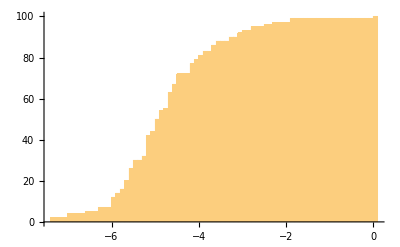

```mathematica
Histogram[Log[Abs[#]]&/@spec,{.1},"CumulativeCount"]
```

```mathematica
hlist=(specAbs=Sort[Log[Abs[#]]&/@spec];Join[{{specAbs_⟦1⟧-1,0}},Transpose[{specAbs,Table[n,{n,1,Length[specAbs]}]}],{{0.5,Length[specAbs]}}]);
```

```mathematica
StringJoin[Table["("<>ToString[N[hlist_⟦n,1⟧]]<>","<>ToString[hlist_⟦n,2⟧]<>")",{n,1,Length[hlist]}]]
```

(-8.34909,0)(-7.34909,1)(-7.34909,2)(-6.96074,3)(-6.96074,4)(-6.5443,5)(-6.2758,6)(-6.2758,7)(-5.98822,8)(-5.98822,9)(-5.91822,10)(-5.9179,11)(-5.9179,12)(-5.83059,13)(-5.83059,14)(-5.75926,15)(-5.75926,16)(-5.65614,17)(-5.65614,18)(-5.62275,19)(-5.62275,20)(-5.55112,21)(-5.55112,22)(-5.52713,23)(-5.52713,24)(-5.52056,25)(-5.52056,26)(-5.44616,27)(-5.44616,28)(-5.43711,29)(-5.43711,30)(-5.25244,31)(-5.25244,32)(-5.19848,33)(-5.19848,34)(-5.18706,35)(-5.18706,36)(-5.17808,37)(-5.12402,38)(-5.12402,39)(-5.12127,40)(-5.12127,41)(-5.11643,42)(-5.00325,43)(-5.00325,44)(-4.96648,45)(-4.96648,46)(-4.92458,47)(-4.92458,48)(-4.90976,49)(-4.90976,50)(-4.88245,51)(-4.88245,52)(-4.85115,53)(-4.85115,54)(-4.77801,55)(-4.69699,56)(-4.69699,57)(-4.6674,58)(-4.6674,59)(-4.62816,60)(-4.62816,61)(-4.62652,62)(-4.62652,63)(-4.54916,64)(-4.54916,65)(-4.52442,66)(-4.52442,67)(-4.49508,68)(-4.46083,69)(-4.46083,70)(-4.40055,71)(-4.40055,72)(-4.15137,73)(-4.15137,74)(-4.146,75)(-4.12802,76)(-4.12802,77)(-4.06381,78)(-4.06381,79)(-3.9876,80)(-3.9876,81)(-3.80398,82)(-3.80398,83)(-3.65047,84)(-3.6486,85)(-3.6486,86)(-3.51489,87)(-3.51489,88)(-3.20646,89)(-3.20646,90)(-3.09113,91)(-3.09113,92)(-2.92755,93)(-2.74722,94)(-2.74722,95)(-2.40186,96)(-2.23754,97)(-1.89925,98)(-1.89925,99)(0.,100)(0.5,100)

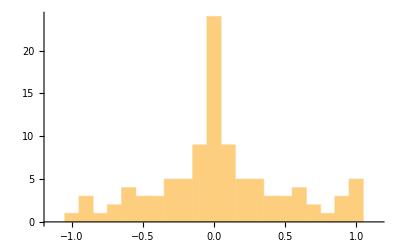

```mathematica
Histogram[Arg[#]/π&/@spec,{-1.15,1.15,.1}]
```

```mathematica
hlist=(specArg=Sort[Arg[#]/π&/@spec];Join[{{-1.15,0}},Transpose[{specArg,Table[n,{n,1,Length[specArg]}]}],{{1.5,Length[specArg]}}]);
```

```mathematica
StringJoin[Table["("<>ToString[N[hlist_⟦n,1⟧]]<>","<>ToString[hlist_⟦n,2⟧]<>")",{n,1,Length[hlist]}]]
```

(-1.15,0)(-0.9568,1)(-0.912403,2)(-0.90976,3)(-0.883382,4)(-0.837933,5)(-0.706174,6)(-0.705283,7)(-0.644856,8)(-0.644101,9)(-0.566903,10)(-0.550567,11)(-0.486155,12)(-0.477502,13)(-0.473075,14)(-0.416903,15)(-0.397452,16)(-0.373947,17)(-0.344811,18)(-0.344597,19)(-0.297306,20)(-0.265754,21)(-0.254992,22)(-0.243322,23)(-0.201953,24)(-0.16838,25)(-0.163838,26)(-0.154926,27)(-0.134696,28)(-0.133429,29)(-0.11351,30)(-0.100821,31)(-0.0966107,32)(-0.0698564,33)(-0.0678109,34)(-0.061483,35)(-0.052327,36)(-0.0464028,37)(-0.0436202,38)(-0.0324675,39)(-0.0312115,40)(-0.016888,41)(-0.0117123,42)(-0.00897276,43)(-0.00799489,44)(0.,45)(0.,46)(0.,47)(0.,48)(0.,49)(0.,50)(0.,51)(0.,52)(0.00799489,53)(0.00897276,54)(0.0117123,55)(0.016888,56)(0.0312115,57)(0.0324675,58)(0.0436202,59)(0.0464028,60)(0.052327,61)(0.061483,62)(0.0678109,63)(0.0698564,64)(0.0966107,65)(0.100821,66)(0.11351,67)(0.133429,68)(0.134696,69)(0.154926,70)(0.163838,71)(0.16838,72)(0.201953,73)(0.243322,74)(0.254992,75)(0.265754,76)(0.297306,77)(0.344597,78)(0.344811,79)(0.373947,80)(0.397452,81)(0.416903,82)(0.473075,83)(0.477502,84)(0.486155,85)(0.550567,86)(0.566903,87)(0.644101,88)(0.644856,89)(0.705283,90)(0.706174,91)(0.837933,92)(0.883382,93)(0.90976,94)(0.912403,95)(0.9568,96)(1.,97)(1.,98)(1.,99)(1.,100)(1.5,100)

### Word translation

#### Bulk vectors

```mathematica
EnglishRef=TopicClustersEnglish;
```

```mathematica
GermanRef=TopicClustersGerman;
```

```mathematica
PandPChapEnglish=StringSplit[ExampleData[{"Text","PrideAndPrejudice"}],"Chapter "~~DigitCharacter..~~" "];
```

```mathematica
Length[PandPChapEnglish]
```

61

```mathematica
VecEnglish=Table[{EnglishRef_⟦k,1⟧,StringCount[PandPChapEnglish,WordBoundary~~Alternatives@@(#_⟦1⟧&/@EnglishRef_⟦k,1⟧)~~WordBoundary,IgnoreCase->True]},{k,1,Length[EnglishRef]}];
```

```mathematica
PandPChapGerman=StringReplace[ImportString[#,"HTML"]&/@StringReplace[StringReplace[StringReplace[StringSplit[Import["Stolz und Vorurteil (2) Grawe.txt"],"Kapitel "~~("l"|DigitCharacter)..],{"<":>"< ","\n":>"\n舜"}],{(s:("舜"~~Repeated[Except["\n"],{1,50}]))~~"\n":>s<>"垚"}],{"舜":>""}],{"垚":>"\n\n","^":>""}];
```

```mathematica
Length[PandPChapGerman]
```

61

```mathematica
VecGerman=Table[{GermanRef_⟦k,1⟧,StringCount[PandPChapGerman,WordBoundary~~Alternatives@@(#_⟦1⟧&/@GermanRef_⟦k,1⟧)~~WordBoundary,IgnoreCase->True]},{k,1,Length[GermanRef]}];
```

```mathematica
FlatScreenedPairs=Flatten[Table[{#_⟦1⟧,#_⟦2,k⟧},{k,1,Length[#_⟦2⟧]}]&/@Select[Table[{EnglishRef[[k,1]],#_⟦1⟧&/@Select[VecGerman,JaccardRuzickaSim[#_⟦2⟧,Cases[VecEnglish,{EnglishRef[[k,1]],___}]_⟦1,2⟧]≥Max[1-7/100*√61,1-√(Length[Select[Min[#]&/@Transpose[{#_⟦2⟧,Cases[VecEnglish,{EnglishRef[[k,1]],___}]_⟦1,2⟧}],#>0&]]/Total[Max[#]&/@Transpose[{#_⟦2⟧,Cases[VecEnglish,{EnglishRef[[k,1]],___}]_⟦1,2⟧}]])]&]},{k,1,Length[EnglishRef]}],Length[#_⟦2⟧]>0&],1];
```

```mathematica
SiftedTags=Union[(#_⟦1⟧&/@FlatScreenedPairs)];SiftedEnglishRef=Reverse[SortBy[Table[Cases[EnglishRef,{SiftedTags[[k]],___}]_⟦1⟧,{k,1,Length[SiftedTags]}],#_⟦3⟧&]];
```

```mathematica
SiftedTags=Union[(#_⟦2⟧&/@FlatScreenedPairs)];SiftedGermanRef=Reverse[SortBy[Table[Cases[GermanRef,{SiftedTags[[k]],___}]_⟦1⟧,{k,1,Length[SiftedTags]}],#_⟦3⟧&]];
```

```mathematica
Length[SiftedEnglishRef]
```

101

```mathematica
Length[SiftedGermanRef]
```

99

#### Spectral parameters for English

```mathematica
FromTopics=SiftedEnglishRef;
```

```mathematica
FromDelta=ReadDelta[#]&/@FromTopics;
```

```mathematica
FromN=(#_⟦3⟧-1)&/@FromTopics;
```

```mathematica
AbsoluteTiming[KinSpecSWLongTag[TopicClustersEnglish,PenTopic,#_⟦1⟧&/@FromTopics];]
```

{55.8926,Null}

```mathematica
FromKinQ=KinQ;
```

```mathematica
FromEta=SemanticComplexities;
```

#### Spectral parameters for German

```mathematica
ToTopicsGerman=SiftedGermanRef;
```

```mathematica
Length[ToTopicsGerman]
```

99

```mathematica
ToDeltaGerman=ReadDelta[#]&/@ToTopicsGerman;
```

```mathematica
ToNGerman=(#_⟦3⟧-1)&/@ToTopicsGerman;
```

```mathematica
AbsoluteTiming[KinSpecSWLongTag[TopicClustersGerman,PdeTopic,#_⟦1⟧&/@ToTopicsGerman];]
```

{77.3777,Null}

```mathematica
ToKinGerman=KinQ;
```

```mathematica
ToEtaGerman=SemanticComplexities;
```

#### Translation

```mathematica
AbsoluteTiming[fromLabeled=Transpose[{#_⟦1⟧&/@FromTopics,FromKinQ}];toLabeled=Transpose[{#_⟦1⟧&/@ToTopicsGerman,ToKinGerman}];Report=Table[{FlatScreenedPairs_⟦k⟧,(JaccardRuzickaSim[Cases[fromLabeled,{FlatScreenedPairs_⟦k,1⟧,_}]_⟦1,2⟧,Cases[toLabeled,{FlatScreenedPairs_⟦k,2⟧,_}]_⟦1,2⟧])},{k,1,Length[FlatScreenedPairs]}];]
```

{0.0146899,Null}

```mathematica
prep=Union[Select[Table[{Report_⟦n,1,1⟧,Report_⟦n,1,2⟧,Report_⟦n,2⟧},{n,1,Length[Report]}],#_⟦3⟧≥0.7&]];g=Graph[(#_⟦1⟧->#_⟦2⟧)&/@prep,EdgeWeight->(#_⟦3⟧&/@prep)];(KuhnSln={#,FindRowRank[#,prep],FindColRank[#,prep]}&/@Select[{#,PropertyValue[{g,#},EdgeWeight]}&/@FindIndependentEdgeSet[g],#_⟦2⟧>0&])//TableForm
```

{{Brighton,24}}->{{brighton,25}}
0.78634126765527 | 1 | 1
{{de,39}}->{{bourgh,36},{bourghs,4}}
0.92037216810033 | 1 | 2
{{Bourgh,35},{Bourgh's,4}}->{{de,40}}
0.91504854679526 | 2 | 1
{{Derbyshire,24}}->{{derbyshire,23},{derbyshires,1}}
0.90046246124988 | 1 | 1
{{five,30}}->{{fünftausend,2},{fünfundzwanzig,2},{fünf,24},{fünften,1}}
0.8473591399164 | 1 | 1
{{impossible,44}}->{{unmöglich,29},{unmöglicher,1},{unmögliches,1}}
0.84698890623081 | 1 | 1
{{library,23}}->{{bibliothek,22},{familienbibliothek,1}}
0.91840486301502 | 1 | 1
{{London,55}}->{{london,103},{londons,3},{londoner,4}}
0.85937945335524 | 1 | 1
{{Meryton,57}}->{{meryton,58},{merytons,1}}
0.87511190099031 | 1 | 1
{{money,26}}->{{geld,29}}
0.85511543635219 | 1 | 1
{{Mr,786}}->{{herr,21},{herren,36},{herrn,20},{mr,830}}
0.88751240152105 | 1 | 1
{{Mrs,343}}->{{mrs,342}}
0.92466319030676 | 1 | 1
{{Netherfield,73}}->{{netherfield,72}}
0.86800460752918 | 1 | 1
{{park,22}}->{{park,23},{parks,4}}
0.87044700889489 | 1 | 1
{{Pemberley,53}}->{{pemberley,52},{pemberleys,2}}
0.913873101622 | 1 | 1
{{pounds,24}}->{{pfund,27}}
0.91778083899624 | 1 | 1
{{Rosings,49}}->{{rosings,48}}
0.83722518292836 | 1 | 1
{{sir,78}}->{{sir,58}}
0.90660068622579 | 2 | 1
{{William,40},{William's,6}}->{{william,40},{williams,5}}
0.92399389552321 | 1 | 1
{{ball,34},{balls,8}}->{{bälle,6},{bällen,2},{balles,1},{bälde,1},{ball,40}}
0.92361523667621 | 1 | 1
{{Catherine,110},{Catherine's,16}}->{{lady,137}}
0.92951414577274 | 1 | 1
{{Charlotte,68},{Charlotte's,17}}->{{charlotte,73},{charlottes,16}}
0.88094757003363 | 1 | 1
{{Collins,156},{Collins's,24}}->{{collins,188}}
0.93871484137497 | 1 | 1
{{colonel,65},{colonel's,1}}->{{oberst,65},{obersten,1}}
0.79043502590936 | 1 | 1
{{Darcy,374},{Darcy's,44}}->{{darcy,384},{darcys,53}}
0.91743360921904 | 1 | 1
{{dinner,33},{dinners,2}}->{{teetassen,1},{aß,2},{aßen,1},{essen,34},{essens,4},{gegessen,1},{isst,2},{ostern,3}}
0.87344469027759 | 1 | 1
{{door,32},{doors,8}}->{{tor,5},{torheit,2},{torheiten,1},{tür,31},{tore,2},{toren,1},{türen,3}}
0.86947628565102 | 1 | 1
{{estate,20},{estates,4}}->{{erbbedingungen,1},{erbvertrag,2},{bewerben,2},{bewerber,1},{erbe,5},{erben,3},{erbin,1},{erbes,1},{erbosen,1},{erbt,1},{erbte,2},{geerbt,2}}
0.90039695140495 | 1 | 1
{{father,116},{father's,19}}->{{vater,114},{väter,1},{vaters,26},{väterliche,1},{väterlichen,1}}
0.91659521823079 | 1 | 1
{{four,33},{four-and-twenty,1}}->{{vier,23},{vierspänner,2},{viertausend,2}}
0.91303449576356 | 1 | 1
{{girl,38},{girls,45}}->{{hausmädchen,2},{mädchen,75},{mädchens,1}}
0.83727236084285 | 1 | 1
{{Jane,263},{Jane's,28}}->{{jane,273},{janes,41}}
0.94798101914595 | 1 | 1
{{Kitty,69},{Kitty's,2}}->{{kitty,66},{kittys,6}}
0.93339464391522 | 1 | 1
{{Lizzy,95},{Lizzy's,2}}->{{lizzy,96},{lizzys,1}}
0.96077074454372 | 1 | 1
{{Lydia,133},{Lydia's,38}}->{{lydia,156},{lydias,35}}
0.91716954094569 | 1 | 1
{{Mary,38},{Mary's,1}}->{{mary,38}}
0.89836933464577 | 1 | 1
{{poor,38},{poorly,3}}->{{arm,5},{arme,19},{armen,11},{armee,1},{armer,2},{ärmer,1},{umarmte,4}}
0.81402179788574 | 1 | 1
{{regiment,19},{regiment's,3}}->{{regiment,33},{regiments,4}}
0.7794501196437 | 1 | 1
{{room,112},{rooms,8}}->{{ankleidezimmer,4},{frauenzimmer,1},{schlafzimmer,1},{schlafzimmers,1},{wohnzimmer,18},{wohnzimmern,1},{wohnzimmerfenster,2},{vorzimmer,3},{zimmer,71},{zimmers,4},{zimmern,1},{geziemenden,2}}
0.85322463477299 | 1 | 1
{{serious,24},{seriously,13}}->{{ernst,27},{ernsthaft,16},{ernsthafte,1},{ernsthaften,3},{ernsthafter,2},{ernsthaftes,1},{ernsthaftigkeit,2},{ernste,3},{ernstem,1},{ernsten,1},{ernster,4},{ernstere,1},{ernsterer,1},{ernstes,4}}
0.85659148517801 | 1 | 1
{{surprise,37},{surprised,35}}->{{überraschend,3},{überrascht,35},{überraschte,4},{überraschung,28},{herrisch,1},{rasenflächen,1}}
0.84893892253657 | 1 | 1
{{table,28},{tables,3}}->{{schreibtisch,1},{spieltische,1},{tisch,29},{tischchen,1},{tischen,1},{tisches,2}}
0.79336882157321 | 1 | 1
{{Wickham,162},{Wickham's,32}}->{{wickham,165},{wickhams,37}}
0.86043031065383 | 1 | 1
{{window,16},{windows,6}}->{{fenster,20},{finster,2},{finsteren,1},{finsterer,2}}
0.92109995101202 | 1 | 1
{{aunt,78},{aunt's,6},{aunts,1}}->{{tante,92},{tanten,1}}
0.87179628791974 | 1 | 1
{{Bennet,294},{Bennet's,29},{Bennets,10}}->{{bennet,297},{bennets,41}}
0.95014446069821 | 1 | 1
{{book,16},{books,13},{book-room,1}}->{{buch,14},{bücher,12},{büchern,2},{bücherei,1}}
0.7862870690514 | 1 | 1
{{child,14},{children,25},{childhood,1}}->{{patenkind,2},{kinderzeit,1},{kindlichen,1},{kind,31},{kindheit,4},{kinder,15},{kindern,10},{kinderstube,1}}
0.82233292014092 | 1 | 1
{{cousin,41},{cousin's,8},{cousins,11}}->{{cousine,26},{cousinen,9}}
0.89617799652298 | 1 | 1
{{Eliza,22},{Elizabeth,597},{Elizabeth's,38}}->{{elizabeth,640},{elizabeths,37}}
0.84058268495217 | 1 | 1
{{evening,72},{evening's,2},{evenings,4}}->{{abend,60},{abends,25},{abende,4},{abendessen,2},{abendlichen,2}}
0.75979521008603 | 1 | 1
{{Forster,38},{Forster's,1},{Forsters,1}}->{{forster,42},{forsters,3}}
0.77218523297179 | 1 | 1
{{Gardiner,84},{Gardiner's,13},{Gardiners,6}}->{{gardiner,89},{gardiners,16}}
0.90490706324588 | 1 | 1
{{letter,115},{letters,16},{letter-paper,1}}->{{briefeschreiben,2},{briefwechsel,2},{dankbrief,1},{dankesbrief,2},{glückwunschbrief,1},{brief,110},{briefe,15},{briefen,4},{briefes,14}}
0.93094190459007 | 1 | 1
{{man,145},{man's,5},{men,33}}->{{leute,44},{leuten,12},{mann,137},{männer,24},{männern,4},{mannes,25}}
0.87614113127557 | 1 | 1
{{maternal,2},{mother,110},{mother's,25}}->{{mama,11},{mutter,142},{mütterlichen,1}}
0.91764524186405 | 1 | 1
{{nephew,20},{nephew's,2},{nephews,2}}->{{neffe,7},{neffen,19}}
0.90322524292212 | 1 | 1
{{Phillip's,1},{Phillips,26},{Phillips's,5}}->{{philips,40}}
0.87537583431256 | 1 | 1
{{read,40},{reading,14},{reader,3}}->{{las,20},{lies,2},{lese,4},{lasen,1},{last,3},{lesen,19},{überlas,1},{abzulesen,1},{durchzulesen,1},{gelesen,10},{leser,1},{leserin,2},{losgeworden,1},{weiterlese,1},{liest,2}}
0.80341977331838 | 1 | 1
{{uncle,59},{uncle's,9},{uncles,3}}->{{onkel,63},{onkels,17}}
0.86098767218698 | 1 | 1
{{year,28},{years,33},{years',2}}->{{ehejahren,1},{frühjahr,5},{jahreszeit,5},{jahr,29},{jahre,17},{jahren,14},{jahres,3},{jahrelang,2},{jahrelange,1},{jahrelangen,1},{jahrelanges,1}}
0.9181286247227 | 1 | 1
{{young,130},{younger,30},{youngest,13}}->{{jungverheiratet,1},{junggeselle,1},{jüngste,8},{jüngsten,5},{jung,5},{junge,43},{jungen,74},{junger,18},{jünger,3},{jüngere,3},{jüngeren,24},{jüngerer,1},{junges,1}}
0.90908851630589 | 1 | 1
{{best,41},{better,92},{good,184},{good-humoured,6}}->{{gutging,2},{gutteil,2},{gutgehen,1},{gutgeht,1},{gutmütige,1},{gutmütigen,2},{besser,52},{gut,149},{bessere,3},{gute,44},{güte,16},{gutem,6},{besseren,4},{guten,31},{besserer,1},{guter,22},{güter,1},{besseres,6},{gutes,17},{bessern,2},{beste,16},{besten,40},{bester,6},{gebessert,1},{zugute,3},{biss,1},{bisschen,15},{bissig,1},{biest,1}}
0.73741010136298 | 1 | 1
{{Bingley,257},{Bingley's,49},{Bingleys,4},{Bingleys',1}}->{{bingley,269},{bingleys,61}}
0.88593191740184 | 1 | 1
{{brother,62},{brotherly,2},{brother's,13},{brothers,2}}->{{bruder,46},{brüder,2},{bruders,15},{brüderliche,1},{brüderlichen,1}}
0.85776616988654 | 1 | 1
{{daily,3},{day,130},{day's,4},{days,30}}->{{rache,2},{rächt,1},{richten,3},{angerichtet,5},{anrichten,2},{ausrichten,2},{auszurichten,2},{eingerichtet,2},{eingerichteten,1},{einrichten,2},{gericht,4},{gerichtet,10},{gerichteten,2},{herzurichten,1},{nachricht,30},{nachrichten,17},{richter,3},{richtet,1},{richtete,8},{richteten,4},{richtig,24},{richtigkeit,2},{richtige,7},{richtigen,1},{roch,1},{geruch,1},{gerücht,10}}
0.89617694394899 | 1 | 1
{{dance,31},{danced,12},{dances,10},{dancing,21}}->{{durchgetanzt,1},{getanzt,6},{tanz,8},{tänze,10},{tanzen,35},{tanzenden,1},{tänzer,2},{tänzerin,1},{tanzt,3},{tanzte,7},{tanzten,4}}
0.76059412672982 | 1 | 1
{{daughter,78},{daughter's,7},{daughters,49},{daughters',1}}->{{lieblingstochter,2},{tochter,89},{töchter,54},{töchtern,7},{töchterschar,1}}
0.92517649864472 | 1 | 1
{{enter,12},{entered,36},{entrance,12},{entrance-hall,1}}->{{eintrat,8},{eintraten,3},{einträten,1},{eintreten,6},{eintretende,1},{trat,15},{traten,6},{treten,2},{austritt,1},{eintritt,16}}
0.83127653413149 | 1 | 1
{{fortune,39},{fortunes,1},{fortunate,15},{fortunately,2}}->{{urteilsvermögen,2},{vermögen,27},{vermögens,3},{vormund,2},{vormünder,2}}
0.85170775992277 | 1 | 1
{{handsome,37},{handsomely,2},{handsomer,3},{handsomest,4}}->{{hübsch,28},{hübsche,3},{hübscher,3},{hübschere,1},{hübscheren,1},{hübsches,4},{hübscheste,2}}
0.85112029931938 | 1 | 1
{{honour,42},{honoured,9},{honours,2},{honourable,6}}->{{ehrenschulden,2},{ehrenwort,2},{ehrfurcht,1},{ehrgefühl,2},{familienehre,1},{sosehr,5},{verwehrt,1},{ehre,46},{ehren,1},{ehrenvolle,1},{ehrt,2},{geehrt,1},{geehrter,1}}
0.82231352876124 | 1 | 1
{{look,57},{looked,74},{looking,29},{looks,12}}->{{blickweite,1},{rundblick,1},{scharfblick,3},{augenblick,41},{augenblicks,2},{augenblicke,3},{augenblicken,2},{augenblicklich,11},{augenblickliche,1},{anblick,13},{aufblicken,2},{ausblick,2},{blick,54},{blicke,2},{blicken,9},{blickte,12},{blickten,1},{durchblick,1},{durchblicke,1},{hinblick,10}}
0.84805512446976 | 1 | 1
{{Lucas,65},{Lucas's,5},{Lucases,13},{Lucases',1}}->{{lucas,75}}
0.87367489384771 | 1 | 1
{{admire,18},{admired,12},{admires,2},{admiring,2},{admirer,3}}->{{bewundere,3},{bewunderers,1},{bewundern,7},{bewundernden,1},{bewundert,6},{bewunderte,6},{bewunderung,15},{bewundernswerter,2}}
0.89370113157592 | 1 | 1
{{carriage,44},{carriages,6},{carried,8},{carry,5},{carrying,4}}->{{kutsche,48},{kutscher,1},{kutschers,1},{kutschern,1}}
0.86782630471147 | 1 | 1
{{comfort,31},{comforted,1},{comforts,4},{comfortable,12},{comfortably,2}}->{{hinwegtrösten,1},{getröstet,1},{trost,24},{tröste,1},{trösten,10},{trostes,1},{tröstete,3},{trösteten,1},{tröstlich,3},{tröstliche,1}}
0.88705094227303 | 1 | 1
{{disappoint,2},{disappointed,12},{disappointing,3},{disappointment,17},{disappointments,1}}->{{enttäuschen,6},{enttäuschend,1},{enttäuscht,10},{enttäuschten,2},{enttäuschung,20},{enttäuschungen,1}}
0.93826146905783 | 1 | 1
{{happily,5},{happiness,72},{happy,83},{happier,3},{happiest,10}}->{{glückschancen,1},{glück,91},{glücks,9},{glückwunsch,3},{glückwünsche,9},{glückwünschen,2}}
0.86669128308324 | 1 | 1
{{house,106},{houses,4},{household,1},{housemaid,2},{housemaids,1}}->{{hausmädchen,2},{haus,86},{häuschen,2},{hause,56},{haushalt,4},{haushalten,1},{haushälterin,16}}
0.80450497794845 | 1 | 1
{{invite,6},{invited,11},{inviting,3},{invitation,34},{invitations,1}}->{{einzuladen,5},{geladen,1},{überladen,1},{einlud,3},{einladen,5},{einladenden,1},{lud,5},{laden,3},{lodge,9},{einladung,36},{einladungen,2},{einladungskarten,1}}
0.91156968390218 | 1 | 1
{{knew,58},{know,238},{knowing,27},{known,57},{knows,9}}->{{weißt,17},{weiß,80},{weiße,1},{wisse,3},{wusste,69},{wüsste,7},{wissen,71},{wissens,1},{wussten,9},{wüssten,2},{gewiss,19},{gewissheit,4},{gewusst,18},{gewisse,7},{gewissen,15},{gewissenhafter,1},{gewissens,1},{gewisser,2},{gewisses,2}}
0.74766005858734 | 1 | 1
{{laugh,18},{laughed,11},{laughing,10},{laughingly,2},{laughter,2}}->{{lächerlich,7},{lächerlichkeit,1},{lächerlichkeiten,1},{auslachen,2},{gelacht,3},{lach,2},{lachst,1},{lache,4},{lachen,20},{lachend,4},{lachten,1}}
0.92232148423191 | 1 | 1
{{length,32},{long,114},{longed,9},{longing,2},{longer,44}}->{{langeweile,2},{zeitlang,6},{jahrelang,2},{jahrelange,1},{jahrelangen,1},{jahrelanges,1},{lang,32},{längst,3},{long,14},{lange,77},{länge,3},{langem,4},{langen,10},{länger,21},{längerem,3},{längerer,1},{langes,3},{langt,1}}
0.80616423612113 | 1 | 1
{{miss,283},{missed,3},{missing,1},{missent,2},{missish,1}}->{{miss,264},{misses,4}}
0.88288649674711 | 1 | 1
{{pride,47},{prided,1},{proud,22},{proudly,1},{proudest,1}}->{{familienstolz,1},{stolz,67},{stolze,1},{stolzen,3},{stolzes,1},{überstolz,1},{stolzierte,2}}
0.90069894468968 | 1 | 1
{{serve,2},{serving,1},{servant,15},{servant's,2},{servants,12}}->{{liebesdienst,1},{dienst,1},{dienen,1},{diener,14},{dieners,4},{dienerin,1},{dienern,2},{dient,1},{diente,1}}
0.74827702445604 | 1 | 1
{{office,6},{officer,8},{officers,29},{officers',2},{officiousness,1},{officious,3}}->{{offizierspatent,2},{offizier,9},{offiziere,16},{offizieren,13},{offiziersfrauen,1}}
0.73902015876574 | 1 | 1
{{visit,51},{visited,4},{visiting,5},{visits,5},{visitor,11},{visitors,14}}->{{besuch,56},{besuche,4},{besuchen,23},{besucher,10},{besuchers,2},{besucherin,1},{besuchern,1},{besuches,5},{besucht,3},{besuchte,2}}
0.92147904354682 | 1 | 1
{{write,39},{writes,1},{writing,12},{written,19},{writer,3},{wrote,21}}->{{briefeschreiben,2},{schreibtisch,1},{abschreiben,1},{beschreiben,7},{schreib,4},{schreibst,2},{schrieb,21},{schreibe,6},{schreiben,32},{schreiber,2},{schreibers,1},{schreiberin,1},{schreibt,10},{zuschreiben,4},{zuzuschreiben,5},{abgeschrieben,1},{zugeschrieben,1},{beschreibung,8},{beschrieb,2},{beschrieben,2},{geschrieben,18},{beschriebene,1}}
0.76000395689929 | 1 | 1
{{mean,34},{meaning,14},{meanly,3},{meanness,1},{means,57},{meant,28},{meanest,1}}->{{anfrage,1},{ausgefragt,1},{frag,1},{fragst,2},{frage,45},{fragen,52},{fragte,45},{fragten,4},{gefragt,9},{nachfrage,1},{nachzufragen,1},{weiterfragen,2}}
0.81580327944825 | 1 | 1

```mathematica
ResiftedTags=Union[(#_⟦1⟧&/@prep)];ResiftedEnglishRef=Reverse[SortBy[Table[Cases[EnglishRef,{ResiftedTags[[k]],___}]_⟦1⟧,{k,1,Length[ResiftedTags]}],#_⟦3⟧&]];
```

```mathematica
ResiftedTags=Union[(#_⟦2⟧&/@prep)];ResiftedGermanRef=Reverse[SortBy[Table[Cases[GermanRef,{ResiftedTags[[k]],___}]_⟦1⟧,{k,1,Length[ResiftedTags]}],#_⟦3⟧&]];
```

```mathematica
SemanticSim={Position[ResiftedEnglishRef,{#_⟦1⟧,___}]_⟦1,1⟧,Position[ResiftedGermanRef,{#_⟦2⟧,___}]_⟦1,1⟧,#_⟦3⟧}&/@prep;
```

```mathematica
OptimalNodes={Position[ResiftedEnglishRef,{#_⟦1,1,1⟧,___}]_⟦1,1⟧,Position[ResiftedGermanRef,{#_⟦1,1,2⟧,___}]_⟦1,1⟧,#_⟦2,1,1⟧,#_⟦3,1,1⟧}&/@KuhnSln;
```

```mathematica
Export["PnP_EnglishGerman.txt","%tournament\n"<>StringJoin[Riffle[Flatten["\\put("<>ToString[1.5+1+4#_⟦2⟧]<>","<>ToString[90-4#_⟦1⟧]<>"){\\color[rgb]"<>ToString[TempRGB[#_⟦3⟧]]<>"{\\rule{4pt}{4pt}}}"&/@SemanticSim],"\n"]]<>"\n%crosshairs\n"<>StringJoin[Riffle["\n%"<>ResiftedEnglishRef[[#_⟦1⟧,1,1,1]]<>"_"<>ResiftedGermanRef[[#_⟦2⟧,1,1,1]]<>"
\\put("<>ToString[1.5+4#_⟦2⟧+3]<>","<>ToString[90-4#_⟦1⟧+2]<>"){\\color{green}\\linethickness{"<>ToString[1.5/#_⟦3⟧]<>"pt}\\line(-1,0){"<>ToString[4#_⟦2⟧-2]<>"}\\linethickness{"<>ToString[1.5/#_⟦4⟧]<>"pt}\\line(0,1){"<>ToString[4#_⟦1⟧-2]<>"}}"&/@OptimalNodes,"\n"]]];
```

#### English labels

```mathematica
FromClusters=ResiftedEnglishRef;
```

```mathematica
ScoredCluster={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧,Total[#_⟦3⟧],#_⟦5⟧}&/@((prep=Transpose[CensorCluster[#_⟦1⟧]];{#_⟦2⟧,prep_⟦1⟧,prep_⟦2⟧,#_⟦3⟧,#_⟦4⟧})&/@FromClusters);
```

```mathematica
EnglishCompress[w_]:=StringReplace[w,{"ai":>"𝔸","ea":>"𝕀","ou":>"𝕌","ee":>"𝔼","oo":>"𝕆"}]
```

```mathematica
EnglishDecompress[w_]:=StringReplace[w,{"𝔸":>"ai","𝕀":>"ea","𝕌":>"ou","𝔼":>"ee","𝕆":>"oo"}]
```

```mathematica
EvenOut[cl_]:=(prep=EnglishCompress[cl_⟦1⟧];L=Max[StringLength[prep]];{#_⟦1⟧<>StringJoin[Table[" ",{L-StringLength[#_⟦1⟧]}]],#_⟦2⟧}&/@Transpose[{prep,cl_⟦2⟧}])
```

```mathematica
SplitEven[ecl_]:=(L=StringLength[ecl_⟦1,1⟧];Table[{m,EnglishDecompress[StringTake[#_⟦1⟧,{m}]],#_⟦2⟧}&/@ecl,{m,1,L}]);
```

```mathematica
MergeStem[spl_]:=SortBy[(prep=ConnectedComponents[Graph[Join[Table[If[(Length[Union[#_⟦2⟧&/@spl_⟦n⟧]]==1)&&(Length[Union[#_⟦2⟧&/@spl_⟦n+1⟧]]==1),spl_⟦n⟧<->spl_⟦n+1⟧,spl_⟦n⟧<->spl_⟦n⟧],{n,1,Length[spl]-1}],{Last[spl]<->Last[spl]}]]];If[Length[#]>1,{{SortBy[Transpose[#]_⟦1⟧,First]_⟦1,1⟧,StringJoin[#1_⟦2⟧&/@SortBy[Transpose[#]_⟦1⟧,First]],Total[#1_⟦3⟧&/@#_⟦1⟧]}},Flatten[#,1]]&/@prep),First]
```

```mathematica
ColSort[col_]:={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧}&/@Reverse[SortBy[{Flatten[Union[#_⟦1⟧]],Union[#_⟦2⟧]_⟦1⟧,Total[#_⟦3⟧],Min[#_⟦4⟧]}&/@(Transpose[#]&/@(ConnectedComponents[Graph[Join[Table[If[col_⟦k,2⟧==col_⟦k+1,2⟧,{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k+1,1⟧,col_⟦k+1,2⟧,col_⟦k+1,3⟧,k+1},{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}],{k,1,Length[col]-1}],{{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}<->{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}}]]])),Last]]
```

```mathematica
CumHeight[cl_]:=(ch=0;s={};For[n=1,n<=Length[cl],n++,{s=Join[s,{{cl_⟦n,1⟧,cl_⟦n,2⟧,cl_⟦n,3⟧,ch}}];ch=ch+cl_⟦n,3⟧}];s)
```

```mathematica
Word2BarChart[cl_]:=CumHeight[#]&/@(ColSort[#]&/@MergeStem[SplitEven[EvenOut[cl]]])
```

```mathematica
Export["EnglishLabels_for_German_PnP.txt",StringJoin[Table[(BCData=Word2BarChart[{ScoredCluster_⟦k,2⟧,ScoredCluster_⟦k,3⟧}];H=ScoredCluster_⟦k,4⟧;"\\put("<>ToString[5-3Total[Max/@StringLength/@(Transpose[#]_⟦2⟧&/@BCData)]]<>","<>ToString[91.75-1.5-4k]<>"){"<>"\\textbf{"<>"\\setlength{\\unitlength}{3pt}"<>StringJoin[hpos=0;Table[hinc=Max[StringLength/@Transpose[BCData_⟦m⟧]_⟦2⟧];hpos=hpos+hinc;Table[If[BCData_⟦m,n,2⟧==" ","","\\BC{"<>ToString[hpos-hinc]<>"}{"<>ToString[N[Round[BCData_⟦m,n,4⟧/H,10^-3]]]<>"}{"<>(ToString[hinc])<>"}{"<>ToString[N[Round[BCData_⟦m,n,3⟧/H,10^-3]]]<>"}{"<>ToUpperCase[BCData_⟦m,n,2⟧]<>"}\n"],{n,1,Length[BCData_⟦m⟧]}],{m,1,Length[BCData]}]])<>"}}\n",{k,1,Length[ScoredCluster]}]]];
```

```mathematica
"EnglishLabels_for_German_PnP.txt"
```

EnglishLabels_for_German_PnP.txt

#### German labels

```mathematica
FromClusters=ResiftedGermanRef;
```

```mathematica
ScoredCluster={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧,Total[#_⟦3⟧],#_⟦5⟧}&/@((prep=Transpose[CensorCluster[#_⟦1⟧]];{#_⟦2⟧,prep_⟦1⟧,prep_⟦2⟧,#_⟦3⟧,#_⟦4⟧})&/@FromClusters);
```

```mathematica
GermanSort[WordFreqList_]:=Transpose[(assoc=<|#_⟦1⟧->#_⟦2⟧&/@Transpose[WordFreqList]|>;{#,assoc[#]}&/@AlphabeticSort[Keys[assoc],"Swedish"])]
```

```mathematica
RemoveExtraSpace[cl_]:=(sp=Max[0,Min[First[#]_⟦1⟧&/@StringPosition[Transpose[cl]_⟦1⟧,Except[" "],1]-1]];Table[{StringDrop[cl_⟦n,1⟧,sp],cl_⟦n,2⟧},{n,1,Length[cl]}])
```

```mathematica
GermanCompress[w_]:=(Lprot=Max[0,Max[Flatten[StringLength/@StringCases[w," "..]]]];StringTake[#,UpTo[Lprot]]<>StringReplace[StringDrop[#,UpTo[Lprot]],{"ie":>"𝕀","ei":>"𝔼","ss":>"𝕊"}]&/@w)
```

```mathematica
GermanDecompress[w_]:=StringReplace[w,{"𝕀":>"ie","𝔼":>"ei","𝕊":>"ss"}]
```

```mathematica
AdmissibleGermanVerbPrefixes=""|"ab"|"an"|"be"|"auf"|"aus"|"bei"|"ein"|"hin"|"hinein"|"hinaus"|"hinauf"|"hinüber"|"herüber"|"her"|"herein"|"herab"|"heran"|"heraus"|"herauf"|"durch"|"mit"|"nach"|"um"|"vor"|"zu"|"zurück"~~""|"zu"|"ge";
```

```mathematica
PadPrefix0[cl_]:=(HeuristicPrefixL=(Max[#]-1)&/@((Last[#]&/@StringPosition[#,WordBoundary~~AdmissibleGermanVerbPrefixes~~WordCharacter,Overlaps->All])&/@cl_⟦1⟧);MaxPrefixL=Max[HeuristicPrefixL];{Table[{StringDrop[cl_⟦1,n⟧,HeuristicPrefixL_⟦n⟧],StringPadLeft[StringTake[cl_⟦1,n⟧,HeuristicPrefixL_⟦n⟧],MaxPrefixL," "]},{n,1,Length[cl_⟦1⟧]}],cl_⟦2⟧})
```

```mathematica
PadPrefix[cl_]:=GermanSort[RefString=RemoveDiacritics[Last[SortBy[#_⟦1⟧&/@cl_⟦1⟧,StringLength[#]&]],Language->"German"];Transpose[Table[prep=SequenceAlignment[RefString,RemoveDiacritics[cl_⟦1,n,1⟧,Language->"German"]];If[Length[prep_⟦1⟧]>1,Lmax=Max[StringLength/@prep_⟦1⟧];{Table[" ",{m,1,Lmax-StringLength[prep_⟦1,2⟧]}]<>cl_⟦1,n,2⟧<>cl_⟦1,n,1⟧,cl_⟦2,n⟧},{cl_⟦1,n,2⟧<>cl_⟦1,n,1⟧,cl_⟦2,n⟧}],{n,1,Length[cl_⟦1⟧]}]]]
```

```mathematica
ClusterCount={{"ausmachen","machen","ausgemacht","mächtigkeiten"},{10,72,83,100}}
```

{{ausmachen,machen,ausgemacht,mächtigkeiten},{10,72,83,100}}

```mathematica
EvenOut[cl_]:=(prep0=PadPrefix[PadPrefix0[cl]];prep=GermanCompress[prep0_⟦1⟧];L=Max[StringLength[prep]];RemoveExtraSpace[{#_⟦1⟧<>StringJoin[Table[" ",{L-StringLength[#_⟦1⟧]}]],#_⟦2⟧}&/@Transpose[{prep,prep0_⟦2⟧}]])
```

```mathematica
EvenOut[ClusterCount]
```

{{     machen      ,72},{     mächtigk𝔼ten,100},{  ausmachen      ,10},{ausgemacht       ,83}}

```mathematica
SplitEven[ecl_]:=(L=StringLength[ecl_⟦1,1⟧];Table[{m,GermanDecompress[StringTake[#_⟦1⟧,{m}]],#_⟦2⟧}&/@ecl,{m,1,L}]);
```

```mathematica
SplitEven[EvenOut[ClusterCount]]//Transpose//TableForm
```

1
 
72 | 2
 
72 | 3
 
72 | 4
 
72 | 5
 
72 | 6
m
72 | 7
a
72 | 8
c
72 | 9
h
72 | 10
e
72 | 11
n
72 | 12
 
72 | 13
 
72 | 14
 
72 | 15
 
72 | 16
 
72 | 17
 
72
1
 
100 | 2
 
100 | 3
 
100 | 4
 
100 | 5
 
100 | 6
m
100 | 7
ä
100 | 8
c
100 | 9
h
100 | 10
t
100 | 11
i
100 | 12
g
100 | 13
k
100 | 14
ei
100 | 15
t
100 | 16
e
100 | 17
n
100
1
 
10 | 2
 
10 | 3
a
10 | 4
u
10 | 5
s
10 | 6
m
10 | 7
a
10 | 8
c
10 | 9
h
10 | 10
e
10 | 11
n
10 | 12
 
10 | 13
 
10 | 14
 
10 | 15
 
10 | 16
 
10 | 17
 
10
1
a
83 | 2
u
83 | 3
s
83 | 4
g
83 | 5
e
83 | 6
m
83 | 7
a
83 | 8
c
83 | 9
h
83 | 10
t
83 | 11
 
83 | 12
 
83 | 13
 
83 | 14
 
83 | 15
 
83 | 16
 
83 | 17
 
83

```mathematica
Last[SplitEven[EvenOut[ClusterCount]]]
```

{{17, ,72},{17,n,100},{17, ,10},{17, ,83}}

```mathematica
MergeStem[spl_]:=SortBy[(prep=ConnectedComponents[Graph[Join[Table[If[(Length[Union[#_⟦2⟧&/@spl_⟦n⟧]]==1)&&(Length[Union[#_⟦2⟧&/@spl_⟦n+1⟧]]==1),spl_⟦n⟧<->spl_⟦n+1⟧,spl_⟦n⟧<->spl_⟦n⟧],{n,1,Length[spl]-1}],{Last[spl]<->Last[spl]}]]];If[Length[#]>1,{{SortBy[Transpose[#]_⟦1⟧,First]_⟦1,1⟧,StringJoin[#1_⟦2⟧&/@SortBy[Transpose[#]_⟦1⟧,First]],Total[#1_⟦3⟧&/@#_⟦1⟧]}},Flatten[#,1]]&/@prep),First]
```

```mathematica
MergeStem[SplitEven[EvenOut[ClusterCount]]]//TableForm
```

1
 
72 | 1
 
100 | 1
 
10 | 1
a
83
2
 
72 | 2
 
100 | 2
 
10 | 2
u
83
3
 
72 | 3
 
100 | 3
a
10 | 3
s
83
4
 
72 | 4
 
100 | 4
u
10 | 4
g
83
5
 
72 | 5
 
100 | 5
s
10 | 5
e
83
6
m
72 | 6
m
100 | 6
m
10 | 6
m
83
7
a
72 | 7
ä
100 | 7
a
10 | 7
a
83
8
ch
265 |  |  | 
10
e
72 | 10
t
100 | 10
e
10 | 10
t
83
11
n
72 | 11
i
100 | 11
n
10 | 11
 
83
12
 
72 | 12
g
100 | 12
 
10 | 12
 
83
13
 
72 | 13
k
100 | 13
 
10 | 13
 
83
14
 
72 | 14
ei
100 | 14
 
10 | 14
 
83
15
 
72 | 15
t
100 | 15
 
10 | 15
 
83
16
 
72 | 16
e
100 | 16
 
10 | 16
 
83
17
 
72 | 17
n
100 | 17
 
10 | 17
 
83

```mathematica
ColSort[col_]:={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧}&/@Reverse[SortBy[{Flatten[Union[#_⟦1⟧]],Union[#_⟦2⟧]_⟦1⟧,Total[#_⟦3⟧],Min[#_⟦4⟧]}&/@(Transpose[#]&/@(ConnectedComponents[Graph[Join[Table[If[col_⟦k,2⟧==col_⟦k+1,2⟧,{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k+1,1⟧,col_⟦k+1,2⟧,col_⟦k+1,3⟧,k+1},{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}],{k,1,Length[col]-1}],{{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}<->{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}}]]])),Last]]
```

```mathematica
ColSort[#]&/@MergeStem[SplitEven[EvenOut[ClusterCount]]]//TableForm
```

1
a
83 | 1
 
182 |  | 
2
u
83 | 2
 
182 |  | 
3
s
83 | 3
a
10 | 3
 
172 | 
4
g
83 | 4
u
10 | 4
 
172 | 
5
e
83 | 5
s
10 | 5
 
172 | 
6
m
265 |  |  | 
7
a
93 | 7
ä
100 | 7
a
72 | 
8
ch
265 |  |  | 
10
t
83 | 10
e
10 | 10
t
100 | 10
e
72
11
 
83 | 11
n
10 | 11
i
100 | 11
n
72
12
 
93 | 12
g
100 | 12
 
72 | 
13
 
93 | 13
k
100 | 13
 
72 | 
14
 
93 | 14
ei
100 | 14
 
72 | 
15
 
93 | 15
t
100 | 15
 
72 | 
16
 
93 | 16
e
100 | 16
 
72 | 
17
 
93 | 17
n
100 | 17
 
72 |

```mathematica
CumHeight[cl_]:=(ch=0;s={};For[n=1,n<=Length[cl],n++,{s=Join[s,{{cl_⟦n,1⟧,cl_⟦n,2⟧,cl_⟦n,3⟧,ch}}];ch=ch+cl_⟦n,3⟧}];s)
```

```mathematica
CumHeight[(ColSort[#]&/@MergeStem[SplitEven[EvenOut[ClusterCount]]])_⟦6⟧]
```

{{{6},m,265,0}}

```mathematica
Word2BarChart[cl_]:=CumHeight[#]&/@(ColSort[#]&/@MergeStem[SplitEven[EvenOut[cl]]])
```

```mathematica
Export["GermanLabels_PnP.txt",StringJoin[Table[(BCData=Word2BarChart[{ScoredCluster_⟦k,2⟧,ScoredCluster_⟦k,3⟧}];H=ScoredCluster_⟦k,4⟧;"\\put("<>ToString[5.25-.25+1+4k]<>","<>ToString[91]<>"){"<>"\\textbf{"<>"\\setlength{\\unitlength}{3pt}"<>StringJoin[hpos=0;Table[hinc=Max[StringLength/@Transpose[BCData_⟦m⟧]_⟦2⟧];hpos=hpos+hinc;Table[If[BCData_⟦m,n,2⟧==" ","","\\BCR{"<>ToString[hpos-hinc]<>"}{"<>ToString[N[Round[BCData_⟦m,n,4⟧/H,10^-3]]]<>"}{"<>(ToString[hinc])<>"}{"<>(temp=StringReplace[ToUpperCase[StringReplace[BCData_⟦m,n,2⟧,"ß":>"𝕊"]],"𝕊":>"ß"];ToString[N[Round[BCData_⟦m,n,3⟧/H*If[temp1=StringReplace[temp,{"Œ":>"OE","Æ":>"AE","ß":>"S"}];RemoveDiacritics[temp1,Language->"German"]==temp1,1,1.3],10^-3]]])<>"}{"<>(If[StringDelete[temp,CharacterRange["A","Z"]]=="",temp,StringReplace[StringReplace[StringReplace[ExportString[temp,"TeX"],"\\ss":>"{\\ss}"],___~~"\\[\\text{":>""],"}\\]"~~___:>""]])<>"}\n"],{n,1,Length[BCData_⟦m⟧]}],{m,1,Length[BCData]}]])<>"}}\n",{k,1,Length[ScoredCluster]}]]];
```

```mathematica
Export["EnglishGerman_Report.txt",{Last[SortBy[#_⟦1,1,1⟧,Last]]_⟦1⟧,Last[SortBy[#_⟦1,1,2⟧,Last]]_⟦1⟧}&/@KuhnSln];
```